# Homogeneous VS Heterogeneous Analysis Notebook

## Héctor Manuel Sánchez Castellanos

## 0. Define Functions

## Libraries

```mathematica
SetDirectory[NotebookDirectory[]]
(*<<SoNA3BSAnalysis`*)
<<PajaroLocoPublic`
<<HypothesisTesting`
(*Quiet[<<EpiSoNA`]*)
Needs["ANOVA`"]
Needs["HypothesisTesting`"]
```

/Users/chipdelmal/Documents/School/Research/G_SoNA3BS/Analysis

## Params

```mathematica
labels=names={"Base","Wolb","RIDL","Fog"};
stagesLabels={"Female","RIDL","Wolbachia","Total"}
scenariosLabels={"HOM","HET"}
labels2=#[[1]]<>#[[2]]&/@Flatten[Transpose/@({ConstantArray[labels,2],{ConstantArray["_HOM",labels//Length],ConstantArray["_HET",labels//Length]}}//Transpose),1]
binsNames=ToExpression/@names;
paperPath=NotebookDirectory[]<>"/"
(*Image Export------------------------------*)
{imageFormat,imageExportSize}={".png",500};
{minEdges,maxEdges}={5,15};
{sampleRate,secondsPerTick}={144,300};
stages={"FemalePopulation","OxitecPopulation","WolbachiaPopulation","AdultPopulation"};
params=StringSplit/@Import[ParentDirectory[]<>"/global.nls"];
{fitEffectivity,wolEffectivity}={ToExpression[Cases[params,{{},{_,"FITNESS_SELECTION_EFFECTIVITY",_}}][[1,2,3]]],ToExpression[Cases[params,{{},{_,"WOLBACHIA_EFFECTIVITY",_}}][[1,2,3]]]};
(*Plots Colors------------------------------*)
{colorsA,colorsB}={{Blue,Red,Green,Orange,Purple,Yellow,Brown,Black},{LightBlue,LightRed,LightGreen,LightOrange,LightPurple,LightYellow,LightBrown,Gray}};
(*Network Measures--------------------------*)
mixFunction=Mean;
imageSize=500;
edgeshape[e_,___]:={Arrowheads[{{.0005,.5}}],Arrow[e]};
varStyle="LineColor";
graphLay={Automatic,"CircularEmbedding","SpringEmbedding"}[[1]];
vSize=.5;
lThick=.001;
labelsSize=20;
clusteringMethod="Modularity";
measures={(*EdgeCount,*)Mean[VertexInDegree[#]]&,(*GraphDensity,*)GlobalClusteringCoefficient,MeanGraphDistance,EdgeConnectivity,GetSmallWorldCoefficient[#,500]&};
```

{Female,RIDL,Wolbachia,Total}

{HOM,HET}

{Base_HOM,Wolb_HOM,RIDL_HOM,Fog_HOM,Base_HET,Wolb_HET,RIDL_HET,Fog_HET}

/Users/chipdelmal/Documents/School/Research/G_SoNA3BS/Analysis/Sustained/

Import::nffil: File not found during Import.

Part::partw: Part 1 of {} does not exist.

ToExpression::notstrbox: {}⟦1,2,3⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 1 of {} does not exist.

ToExpression::notstrbox: {}⟦1,2,3⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

## Package Functions

### Descriptions

```mathematica
(*(*-------------------------------------------------------------------Auxiliary-------------------------------------------------------------------------*)FixBitesListTail::usage="Converts NetLogo bites lists into Mathematica bites lists"
FixBitesListTails::usage="Converts NetLogo experiment bites lists into Mathematica bites lists"
GetExperimentSection::usage="Returns an XML section that is correctly tagged as such"
ConvertTicksToIntegersExperiment::usage="Converts the ticks values to integers in a single experiment"
ConvertTicksToIntegersExperimentsSet::usage="Converts ticks values into integers in an experiments set"
(*-------------------------------------------------------------------ExperimentHeader-------------------------------------------------------------------*)
GetExperimentsSetXMLData::usage="Returns the XML of all the experiments in XML format in the given path (relative to notebook's directory)"
GetExperimentsSetXMLDataAbsolute::usage="Returns the XML of all the experiments in XML format in the given absolute path"
GetExperimentHeader::usage="Returns the header section of an experiment in list form"
GetExperimentHeaderWithFixedDate::usage="Returns the header of an experiment with the date fixed to mathematica standard"
GetExperimentsSetHeader::usage="Returns the header of a set of experiments with the dates as a range (requires that the section is tagged: 'header')"
GetExperimentParameters::usage="Returns the parameters of a given experiment"
GetExperimentsSetParameters::usage="Returns the parameters that define the behavior of a set of experiments with the independent variables ordered (requires that the section is tagged: 'parameters')"
(*-------------------------------------------------------------------DirectContact----------------------------------------------------------------------*)
GetExperimentContactLabels::usage="Returns the names of the individuals involved in contacts situations of an experiment"
GetExperimentsSetContactLabels::usage="Returns the unrepeated names of the individuals involved in contacts situations of a set of experiments"
GetContactTally::usage="Returns the transition contacts counts"
GetExperimentContactsSection::usage="Returns the contacts section of a single experiment"
GetExperimentsSetContactsSection::usage="Returns the contacts section of a set of experiments"
GetExperimentContactsTransitionsWithPattern::usage="Returns the contacts matrix of an experiment given a labels pattern"
GetExperimentSetRawContactsTransitionsWithPattern::usage="Returns the individual contacts matrices of every experiment of a set"
GetExperimentSetContactsTransitionsWithPattern::usage="Returns the contacts matrix of a set of experiments given a labels pattern with the given mix function applied to the matrices"
FilterBetweenTicksExperiment::usage="Filters all the contacts that do not happen between the given ticks period"
FilterBetweenTicksExperimentSet::usage="Filters all the contacts that do not happen between the given ticks period in an experiments set"
GetExperimentSetContactsTransitionsWithPatternInIntervals::usage="Returns the contact matrices divided un fixed time intervals (cumulative)"
(*-------------------------------------------------------------------BitesContact-----------------------------------------------------------------------*)
GetExperimentBiteLabels::usage="Returns the names of the individuals involved in bites situations of an experiment"
GetExperimentsSetBiteLabels::usage="Returns the names of the individuals involved in bites situations of a set of experiments"
GetExperimentBitesSection::usage="Returns the bites section of a single experiment"
GetExperimentsSetBitesSection::usage="Returns the bites section of a set of experiments"
GetBitesLists::usage="Returns the bite lists of the experiments"
GetBitesTransitions::usage="Converts the bite lists into transitions lists"
GetBitesTransitionsCases::usage="Filters the bites in cases"
GetTransitionFrequencies::usage="Returns the transitions frequencies of a list of bites"
GetExperimentTransitionFrequencies::usage="Returns the transitions frequencies of an experiment"
GetExperimentTransitionFrequenciesFromTail::usage="Returns the transitions frequencies of an experiment from the tail section"
GetExperimentBitesTransitionsWithPattern::usage="Returns the bites transitions matrix from an experiment"
GetExperimentsSetRawBitesTransitionsWithPattern::usage="Returns the bites transitions of a set of experiments individualy"
GetExperimentsSetBitesTransitionsWithPattern::usage="Returns the bites transitions from a set of experiments"
(*-------------------------------------------------------------------HousesContact-------------------------------------------------------------------*)
GetExperimentHousesLabels::usage="Returns the names of the houses entities on an experiment"
GetExperimentsSetHousesLabels::usage="Returns the names of the houses entities on the experiments set"
GetHousesContactTally::usage="*Returns the tally of contacts with houses entities"
GetExperimentsSetHousesContactsSection::usage="Returns the houses contacts section of a set of experiments"
GetExperimentHousesContactsTransitionsWithPattern::usage="Returns the houses contacts of an experiment"
GetExperimentsSetHousesContactsTransitionsWithPattern::usage="Returns the houses contacts of an experiments set"
GetExperimentsSetRawHousesContactsTransitionsWithPattern::usage="Returns the individual experiments matrices of an experiments set"
(*-------------------------------------------------------------------PopulationDynamics-------------------------------------------------------------------*)
GetExperimentTicksOutputs::usage="Returns the ticks outputs of an experiment"
GetExperimentsSetTicksOutputs::usage="Returns the ticks outputs of a set of experiments"
GetExperimentOutputTags::usage="Returns the names of the outputs of an experiment"
GetTaggedOutputFromExperimentsIndexes::usage="Returns the tick output of a given XML tag from the samples provided by the list of indexes (on the imported XML list of samples)"
GetExperimentSetIndexPositionsByIndependentVariableValues::usage="Returns the indexes that contain the combination of independent variables values"
GetExperimentSetTaggedOutputByIndependentVariableValues::usage="Returns the tagged output values of the samples that contain the combination of independent variables values (the return list of lists is ordered by ticks)"
GetExperimentSetIndexPositionsByIndependentVariableBins::usage="Returns the indexes (on the imported XML list of samples) from the samples that contain a certain combination of independent variables"
(*-------------------------------------------------------------------SCEIR Dynamics-----------------------------------------------------------------------*)
SCEIRInitializePersonsVectors::usage="Returns the initialized state vectors with the given indexes cases"
SCEIRInitializeCounterVectors::usage="Returns the initialized count vectors with zero values for each of them"
SCEIRInitializeVectors::usage="Initializes both vectors"
SCEIRUpdateCounters::usage="Updates the counters for each of the individuals in each state"
SCEIRTransitionState::usage="Returns the positions of the individuals that should make a transition given a state and threshold for counter"
SCEIRGenerateContagionMatrix::usage="Returns the bool values of the probabilities of an individual infecting the others without taking into account if the individual is himself in Infected state"
SCEIRGeneratePopulationContagionsMatrix::usage="Returns the matrix of the individuals being infected (columns) by others (rows)"
SCEIRUpdatePersonsVectorWithCondemnedIndividuals::usage="Returns the updated population vector with the replaced condemned individuals"
SCEIRSpreadDisease::usage="Spreads the disease between contacts probabilistically according to their contacts matrices"
SCEIRRunEpidemicEpoch::usage="Spread a disease through one epoch between the population in a network"
SCEIRNetworkEpidemicListEpochs::usage="Spreads a disease in a network returning the persons and counter vectors for each epoch"
SCEIRNetworkEpidemic::usage="Spread a disease in a network returning the persons and counter vectors for the last epoch"
SCEIRGenerateListPlotLists::usage="Returns the epidemic process lists so that they can be plotted"
SCEIRGraphEpidemicProcess::usage="Generates a graph of each step of the epidemic process"
SCEIRListPlotEpidemicProcess::usage="Generates a list plot of each step of the epidemic process"
SCEIRMatrixPlots::usage="Generates a Matrix Plot representation of each of the states in the epidemic process"
SCEIRGenerateMatrixPlotMatrices::usage="Generates a full condensed matrix for a matrix plot of the epidemic process"
(*-------------------------------------------------------------------SEIR Dynamics-----------------------------------------------------------------------*)
SEIRInitializePersonsVectors::usage=""
SEIRInitializeCounterVectors::usage=""
SEIRInitializeVectors::usage=""
SEIRUpdateCounters::usage=""
SEIRTransitionState::usage=""
SEIRGenerateContagionMatrix::usage=""
SEIRGeneratePopulationContagionsMatrix::usage=""
SEIRUpdatePersonsVectorWithCondemnedIndividuals::usage=""
SEIRSpreadDisease::usage=""
SEIRRunEpidemicEpoch::usage=""
SEIRNetworkEpidemicListEpochs::usage=""
SEIRNetworkEpidemic::usage=""
SEIRGraphEpidemicProcess::usage=""
SEIRGenerateListPlotLists::usage=""
SEIRListPlotEpidemicProcess::usage=""
SEIRGenerateMatrixPlotMatrices::usage=""
(*-------------------------------------------------------------------SIR Dynamics-----------------------------------------------------------------------*)
SIRInitializePersonsVectors::usage=""
SIRInitializeCounterVectors::usage=""
SIRInitializeVectors::usage=""
SIRUpdateCounters::usage=""
SIRTransitionState::usage=""
SIRGenerateContagionMatrix::usage=""
SIRGeneratePopulationContagionsMatrix::usage=""
SIRUpdatePersonsVectorWithCondemnedIndividuals::usage=""
SIRSpreadDisease::usage=""
SIRRunEpidemicEpoch::usage=""
SIRNetworkEpidemicListEpochs::usage=""
SIRNetworkEpidemic::usage=""
SIRGraphEpidemicProcess::usage=""
SIRGenerateListPlotLists::usage=""
SIRListPlotEpidemicProcess::usage=""
SIRGenerateMatrixPlotMatrices::usage=""
(*-------------------------------------------------------------------SIS Dynamics-----------------------------------------------------------------------*)
SISInitializePersonsVectors::usage=""
SISInitializeCounterVectors::usage=""
SISInitializeVectors::usage=""
SISUpdateCounters::usage=""
SISTransitionState::usage=""
SISGenerateContagionMatrix::usage=""
SISGeneratePopulationContagionsMatrix::usage=""
SISUpdatePersonsVectorWithCondemnedIndividuals::usage=""
SISSpreadDisease::usage=""
SISRunEpidemicEpoch::usage=""
SISNetworkEpidemicListEpochs::usage=""
SISNetworkEpidemic::usage=""
SISGraphEpidemicProcess::usage=""
SISGenerateListPlotLists::usage=""
SISListPlotEpidemicProcess::usage=""
SISGenerateMatrixPlotMatrices::usage=""
(*-------------------------------------------------------------------Wrappers-----------------------------------------------------------------------*)
NetworkEpidemicListEpochs::usage="Simulates an epidemic returning the stages of the process"
GenerateListPlotLists::usage="Generates the list plots lists of the process"
ListPlotEpidemic::usage="Generates the final list plot of the process"
GenerateMatrixPlotMatrix::usage="Generates the final matrix of the process"
MatrixPlotEpidemic::usage="Generates the final matrix plot"
GraphEpidemicProcess::usage="Generates the graphs of each stage of the epidemic process"
ListPlotEpidemicProcess::usage="List plots an epidemic process in each stage"
MatrixPlotEpidemicProcess::usage="Generates the matrix plots at each stage of the process"
(*-------------------------------------------------------------------Graphs-------------------------------------------------------------------------------*)
GraphTransitionsFrequenciesSet::usage="Graphs a transitions frequencies set of matrices scaled to a global max of contacts"
(*-------------------------------------------------------------------Sweeps-------------------------------------------------------------------------------*)
Summary::usage=""
NetworkEpidemicListEpochsRepeatOnIndexes::usage=""
NetworkEpidemicListEpochsRepeatSweep::usage=""
ListPlotRepeatOnIndexes::usage=""
MatrixPlotRepeatOnIndexes::usage=""*)
```

### Auxiliary

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)(*-------------------------------------------------------------------Auxiliary-------------------------------------------------------------------*)FixBitesListTail[experimentTail_]:=(StringReplace[#,{"["->" ","]"->" "," "->","}]//ToString//ToExpression)&/@experimentTail
FixBitesListTails[experimentsTails_]:=FixBitesListTail/@experimentsTails
GetExperimentSection[xmlExperimentData_,sectionTitle_]:=Cases[xmlExperimentData,XMLElement[sectionTitle,_,_],Infinity]
ConvertTicksToIntegersExperiment[cSectExperiment_]:=Module[{cSectOne=cSectExperiment,heads,tails,tailsFixed},heads=cSectOne[[All,1]];
tails=cSectOne[[All,2;;All]];
tailsFixed=Table[{#[[1]],#[[2]]//ToExpression}&/@tails[[i]],{i,1,tails//Length}];
(Prepend[#[[2]],#[[1]]]&/@({heads,tailsFixed}//Transpose))]
ConvertTicksToIntegersExperimentsSet[cSect_]:=ConvertTicksToIntegersExperiment/@cSect
```

### Head

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------ExperimentHeader------------------------------------------------------------*)
GetExperimentsSetXMLData[path_]:=Module[{filesNames,allFilesPaths},allFilesPaths=FileNames["*.xml",Directory[]<>path];
Import/@allFilesPaths]
GetExperimentsSetXMLDataAbsolute[path_]:=Module[{filesNames,allFilesPaths},allFilesPaths=FileNames["*.xml",path];
Import/@allFilesPaths]
GetExperimentHeader[xmlExperimentData_]:=Module[{temp},temp=GetExperimentSection[xmlExperimentData,"header"];
Cases[temp,XMLElement[a_,_,{c_}]->{a,c},{3}]]
GetExperimentHeaderWithFixedDate[xmlExperimentData_]:=Module[{header,datePosition},header=GetExperimentHeader[xmlExperimentData];
datePosition=(Position[header,{"date",_}]//Flatten)[[1]];
ReplacePart[header,{3,2}->DateList[header[[datePosition]][[2]]]]]
GetExperimentsSetHeader[xmlExperimentsDataSet_]:=Module[{headers,datePosition,sorted,dateRange},headers=(GetExperimentHeaderWithFixedDate[#]&/@xmlExperimentsDataSet);
datePosition=(Position[headers[[1]],{"date",_}]//Flatten)[[1]];
sorted=headers[[All,datePosition]][[All,2]]//Sort;
dateRange=DateString/@{sorted//First,sorted//Last};
ReplacePart[headers[[1]],datePosition->{"date",dateRange}]]
GetExperimentParameters[xmlExperimentData_]:=Module[{temp},
temp=GetExperimentSection[xmlExperimentData,"parameters"];
Cases[temp,XMLElement[a_,{"id"->b_},{c_}]->{a,b,c},{3}]
]
GetExperimentsSetParameters[xmlExperimentsDataSet_]:=Module[{experimentsData,independentPositions,independentTriplets,independentRanges,replacementRules},experimentsData=GetExperimentParameters[#]&/@xmlExperimentsDataSet;
independentPositions=Position[experimentsData[[1]],{"independent",_,_}]//Flatten;
independentTriplets=experimentsData[[All,#]]&/@independentPositions;
independentRanges=DeleteDuplicates/@(ToExpression/@(#[[All,3]]&/@independentTriplets));
replacementRules={#[[1]],3}->#[[2]]&/@({independentPositions,independentRanges}//Transpose);
ReplacePart[experimentsData[[1]],replacementRules]
]
```

### Body

```mathematica
FilterBetweenTicksExperiment[fixedTicksCSect_,low_,high_]:=Module[{expCSect=fixedTicksCSect,section},Table[section=expCSect[[i]];
Cases[section[[2;;All]],{a_,b_}/;(b≥low&&b≤high)]//Prepend[#,section[[1]]]&,{i,1,expCSect//Length}]]
FilterBetweenTicksExperimentSet[cSect_,low_,high_]:=FilterBetweenTicksExperiment[#,low,high]&/@cSect
(*DirectContact*)
GetExperimentContactLabels[contactsSection_]:=Module[{b},b=(GetContactTally[#]&/@contactsSection)//Sort[#]&;
b[[All,1]]]
GetExperimentsSetContactLabels[contactsSections_]:=(GetExperimentContactLabels/@contactsSections)//Flatten//DeleteDuplicates//Sort
GetContactTally[contactsSectionPart_]:=Module[{individual,contacts},individual=contactsSectionPart[[All,1]][[1]];
contacts=contactsSectionPart[[All,1]]//Drop[#,1]&//Tally;
{individual,contacts}]
GetExperimentContactsSection[experimentXMLData_]:=GetExperimentsSetContactsSection[{experimentXMLData}][[1]]
GetExperimentsSetContactsSection[experimentsXMLData_]:=Module[{output,bitesListRaw,fixedListsTails},output=GetExperimentSection[#,"output"]&/@experimentsXMLData;
bitesListRaw=Map[Cases[#,XMLElement["output",{"id"->"contactList"},a_]->a]&,output];(*Lists Tails with data in String form*)fixedListsTails=Map[ToString,FixBitesListTails[bitesListRaw],{5}][[All,1]];(*List Tails with data in Data form*)fixedListsTails//ConvertTicksToIntegersExperimentsSet]
GetExperimentContactsTransitionsWithPattern[contactsSection_,pattern_]:=Module[{b,c},b=(GetContactTally[#]&/@contactsSection)//Sort[#]&;
c=Table[If[Count[b[[i,2]],{#,_}]>0,b[[i,2]][[Position[b[[i,2]],#][[1]][[1]],2]],0]&/@pattern,{i,1,pattern//Length}];
{c,pattern}]
GetExperimentSetRawContactsTransitionsWithPattern[contactsSections_,pattern_]:=Module[{contacts},contacts=GetExperimentContactsTransitionsWithPattern[#,pattern]&/@contactsSections;
{contacts[[All,1]],contacts[[1,2]]}]
GetExperimentSetContactsTransitionsWithPattern[contactsSections_,pattern_,mixFunction_]:=Module[{contacts},contacts=GetExperimentContactsTransitionsWithPattern[#,pattern]&/@contactsSections;
{contacts[[All,1]]//mixFunction,contacts[[1,2]]}]
GetExperimentSetContactsTransitionsWithPatternInIntervals[fixedTicksCSect_,labels_,mixFunction_,frames_]:=Module[{max,increment,low,high,fCSect,intervals},max=fixedTicksCSect[[1]][[All,2;;All]][[All,All,2]]//Flatten//Max;
increment=max/frames;
intervals=Table[low=0;high=i;
fCSect=FilterBetweenTicksExperimentSet[fixedTicksCSect,low,high];
GetExperimentSetContactsTransitionsWithPattern[fCSect,labels,mixFunction],{i,0,max,increment}]]
```

### Tail

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------BitesContact-------------------------------------------------------------------*)
GetExperimentBiteLabels[bites_]:=GetExperimentsSetBiteLabels[{bites}]
GetExperimentsSetBiteLabels[bites_]:=Module[{flat},flat=bites//Flatten//DeleteDuplicates;
Cases[flat,a_/;StringMatchQ[a,LetterCharacter..]]//Sort]
GetExperimentBitesSection[experimentXMLData_]:=GetExperimentsSetBitesSection[{experimentXMLData}][[1]]
GetExperimentsSetBitesSection[experimentsXMLData_]:=Module[{output,bitesListRaw,fixedListsTails},output=GetExperimentSection[#,"output"]&/@experimentsXMLData;
bitesListRaw=Map[Cases[#,XMLElement["output",{"id"->"biteList"},a_]->a]&,output];(*Lists Tails with data in String form*)fixedListsTails=Map[ToString,FixBitesListTails[bitesListRaw],{5}][[All,1]];(*List Tails with data in Data form*)fixedListsTails]
GetBitesLists[fixedListsTails_]:=Map[#[[All,1]]&,Map[Drop[#,1]&,#]]&/@fixedListsTails
GetBitesTransitions[bitesLists_]:=((Partition[#,2,1]&/@#)//Flatten[#,1]&)&/@bitesLists
GetBitesTransitionsCases[bitesTransitions_]:=bitesTransitions//Flatten//DeleteDuplicates//Tuples[#,2]&
GetTransitionFrequencies[bitesTransitions_,agentsNames_]:=Module[{matrices},matrices=Table[Table[Count[j,{agentsNames[[i]],#}]&/@agentsNames,{i,1,agentsNames//Length}],{j,bitesTransitions}];
{matrices,ConstantArray[agentsNames,matrices//Length]}//Transpose]
GetExperimentTransitionFrequencies[transitionFrequencies_,mixFunction_]:={transitionFrequencies[[All,1]]//mixFunction,transitionFrequencies[[1,2]]}
GetExperimentTransitionFrequenciesFromTail[fixedListsTails_,pattern_,mixFunction_]:=Module[{bitesLists,bitesTransitions,agentsNames,transitionFrequencies},bitesLists=GetBitesLists[fixedListsTails];
bitesTransitions=GetBitesTransitions[bitesLists];
(*agentsNames=GetAgentsNames[bitesTransitions];*)transitionFrequencies=GetTransitionFrequencies[bitesTransitions,pattern];
GetExperimentTransitionFrequencies[transitionFrequencies,mixFunction]]
GetExperimentBitesTransitionsWithPattern[bitesExperimentList_,pattern_]:=GetExperimentTransitionFrequenciesFromTail[{bitesExperimentList},pattern,Total]
GetExperimentsSetRawBitesTransitionsWithPattern[bitesList_,pattern_]:={(GetExperimentTransitionFrequenciesFromTail[{#},pattern,Total]&/@bitesList)[[All,1]],pattern}
GetExperimentsSetBitesTransitionsWithPattern[bitesList_,pattern_,mixFunction_]:=GetExperimentTransitionFrequenciesFromTail[bitesList,pattern,mixFunction]
(*HouseContact*)
GetExperimentHousesLabels[contactsSection_]:=GetExperimentsSetHousesLabels[{contactsSection}]
GetExperimentsSetHousesLabels[contactsSection_]:=Module[{a,houses},Table[a=GetHousesContactTally[contactsSection[[i]]];
houses=Flatten[a[[All,2]],1][[All,1]]//DeleteDuplicates//Sort,{i,1,contactsSection//Length}]//Flatten//Sort//DeleteDuplicates]
GetHousesContactTally[contactsSectionPart_]:=Module[{housesNames,individualsNames,tallys},housesNames=Table[i[[All,1]],{i,contactsSectionPart[[All,2;;All]]}]//Flatten//DeleteDuplicates//Sort;
individualsNames=contactsSectionPart[[All,1]];
tallys=Tally/@contactsSectionPart[[All,2;;All,1]];
{individualsNames,tallys}//Transpose]
GetExperimentsSetHousesContactsSection[experimentsXMLData_]:=Module[{output,bitesListRaw,fixedListsTails},output=GetExperimentSection[#,"output"]&/@experimentsXMLData;
bitesListRaw=Map[Cases[#,XMLElement["output",{"id"->"contactHousesList"},a_]->a]&,output];(*Lists Tails with data in String form*)fixedListsTails=Map[ToString,FixBitesListTails[bitesListRaw],{5}][[All,1]];(*List Tails with data in Data form*)fixedListsTails]
GetExperimentHousesContactsTransitionsWithPattern[contactsSection_,patternPersons_,patternHouses_]:=Module[{a,persons=patternPersons,houses=patternHouses,partial,matrix,transitions,b,c,labels},a=GetHousesContactTally[contactsSection];
b=a//Sort;
persons=b[[All,1]]//Flatten;
houses=Flatten[a[[All,2]],1][[All,1]]//DeleteDuplicates//Sort;
labels={persons,houses}//Flatten;
partial=Table[If[Count[b[[i,2]],{#,_}]>0,b[[i,2]][[Position[b[[i,2]],#][[1]][[1]],2]],0]&/@labels,{i,1,b//Length}];
matrix={partial,ConstantArray[ConstantArray[0,partial[[1]]//Length],houses//Length]}//Flatten[#,1]&;
transitions={matrix,labels}]
GetExperimentsSetRawHousesContactsTransitionsWithPattern[contactsSection_,patternPersons_,patternHouses_]:=Module[{matrices},matrices=GetExperimentHousesContactsTransitionsWithPattern[#,patternPersons,patternHouses]&/@contactsSection;
{matrices[[All,1]],matrices[[1,2]]}]
GetExperimentsSetHousesContactsTransitionsWithPattern[contactsSection_,patternPersons_,patternHouses_,mixFunction_]:=Module[{matrices},matrices=GetExperimentHousesContactsTransitionsWithPattern[#,patternPersons,patternHouses]&/@contactsSection;
{matrices[[All,1]]//mixFunction,matrices[[1,2]]}]
```

### SIS

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SIS-------------------------------------------------------------------*)
SISInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
{sPersonsVct*(1-iPersonsVct),iPersonsVct}]
SISInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
{sCounterVct,iCounterVct}]
SISInitializeVectors[indexesCases_,populationSize_]:={SIRInitializePersonsVectors[indexesCases,populationSize],SIRInitializeCounterVectors[populationSize]}
SISUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SISTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex-1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex-1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SISGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SISGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[2]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SISUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SISSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SISGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SISGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SISUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SISRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SISUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(I->R)*){personsVcts,counterVcts}=SISTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
(*ContagionProcess*){personsVcts,counterVcts}=SISSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SISNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SISInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SISRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SISNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SISGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Green],Style[#[[3]],Purple]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SISGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SISListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SISListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SISGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Infected"},PlotStyle->{Blue,Green}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SISGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
Total[{suceptible,infected,recovered}]]
```

### SIR

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SIR-------------------------------------------------------------------*)
SIRInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
rPersonsVct=ConstantArray[0,populationSize];
{sPersonsVct*(1-iPersonsVct),iPersonsVct,rPersonsVct}]
SIRInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
rCounterVct=ConstantArray[0,populationSize];
{sCounterVct,iCounterVct,rCounterVct}]
SIRInitializeVectors[indexesCases_,populationSize_]:={SIRInitializePersonsVectors[indexesCases,populationSize],SIRInitializeCounterVectors[populationSize]}
SIRUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SIRTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex+1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex+1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SIRGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SIRGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[2]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SIRSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SIRGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SIRGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SIRRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SIRUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(I->R)*){personsVcts,counterVcts}=SIRTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
(*ContagionProcess*){personsVcts,counterVcts}=SIRSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SIRNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SIRNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SIRGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Green],Style[#[[3]],Purple]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SIRGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SIRListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SIRListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SIRGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Infected","Recovered"},PlotStyle->{Blue,Green,Purple}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SIRGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
Total[{suceptible,infected,recovered}]]
```

### SEIR

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SEIR-------------------------------------------------------------------*)
SEIRInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
ePersonsVct=ConstantArray[0,populationSize];
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
rPersonsVct=ConstantArray[0,populationSize];
{sPersonsVct*(1-iPersonsVct),ePersonsVct,iPersonsVct,rPersonsVct}]
SEIRInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
eCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
rCounterVct=ConstantArray[0,populationSize];
{sCounterVct,eCounterVct,iCounterVct,rCounterVct}]
SEIRInitializeVectors[indexesCases_,populationSize_]:={SEIRInitializePersonsVectors[indexesCases,populationSize],SEIRInitializeCounterVectors[populationSize]}
SEIRUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SEIRTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex+1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex+1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SEIRGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SEIRGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[3]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SEIRSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SEIRGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SEIRGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SEIRRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SEIRUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(E->I->R)*){personsVcts,counterVcts}=SEIRTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
{personsVcts,counterVcts}=SEIRTransitionState[personsVcts,counterVcts,thresholds[[3]],3];
(*ContagionProcess*){personsVcts,counterVcts}=SEIRSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SEIRNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SEIRNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SCEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SEIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SEIRGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Orange],Style[#[[3]],Green],Style[#[[4]],Red]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SEIRGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SEIRListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SEIRListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SEIRGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Exposed","Infected","Recovered"}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SEIRGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,exposed,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
exposed=(#/.{1->0})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[4]]);
Total[{suceptible,exposed,infected,recovered}]]
```

### SCEIR

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SCEIR-------------------------------------------------------------------*)
SCEIRInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
cPersonsVct=ConstantArray[0,populationSize];
ePersonsVct=ConstantArray[0,populationSize];
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
rPersonsVct=ConstantArray[0,populationSize];
{sPersonsVct*(1-iPersonsVct),cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct}]
SCEIRInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
cCounterVct=ConstantArray[0,populationSize];
eCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
rCounterVct=ConstantArray[0,populationSize];
{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct}]
SCEIRInitializeVectors[indexesCases_,populationSize_]:={SCEIRInitializePersonsVectors[indexesCases,populationSize],SCEIRInitializeCounterVectors[populationSize]}
SCEIRUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SCEIRTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex+1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex+1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SCEIRGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SCEIRGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[4]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SCEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SCEIRSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SCEIRGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SCEIRGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SCEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SCEIRRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SCEIRUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(C->E->I->R)*){personsVcts,counterVcts}=SCEIRTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
{personsVcts,counterVcts}=SCEIRTransitionState[personsVcts,counterVcts,thresholds[[3]],3];
{personsVcts,counterVcts}=SCEIRTransitionState[personsVcts,counterVcts,thresholds[[4]],4];
(*ContagionProcess*){personsVcts,counterVcts}=SCEIRSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SCEIRNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SCEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SCEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SCEIRNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SCEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SCEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SCEIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SCEIRGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Orange],Style[#[[3]],Green],Style[#[[4]],Red],Style[#[[5]],Purple]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SCEIRGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SCEIRListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SCEIRListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SCEIRGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Condemned","Exposed","Infected","Recovered"}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SCEIRMatrixPlots[epidemicSCEIR_]:=Table[i//MatrixPlot,{i,(epidemicSCEIR[[1]]//Transpose)}]
SCEIRGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,condemned,exposed,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
condemned=(#/.{1->-5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
exposed=(#/.{1->0})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[4]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[5]]);
Total[{suceptible,condemned,exposed,infected,recovered}]]
```

### Graphs

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------Graphs-------------------------------------------------------------------*)
Options[GraphTransitionsFrequenciesSet]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic}}
GraphTransitionsFrequenciesSet[matricesSet_,OptionsPattern[]]:=GraphTransitionsFrequenciesWithMax[#,matricesSet[[All,1]]//Flatten//Max,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle],GraphLayout->OptionValue[GraphLayout],ImageSize->OptionValue[ImageSize],VertexSize->OptionValue[VertexSize],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@matricesSet
```

### Epidemic Wrappers

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------EpidemicWrappers---------------------------------------------------------*)
NetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs],"SIR",SIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs],"SEIR",SEIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs],"SCEIR",SCEIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs]]]
GenerateListPlotLists[epidemicData_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SIRGenerateListPlotLists[epidemicData[[1]]],"SIR",SIRGenerateListPlotLists[epidemicData[[1]]],"SEIR",SEIRGenerateListPlotLists[epidemicData[[1]]],"SCEIR",SCEIRGenerateListPlotLists[epidemicData[[1]]]]]
Options[ListPlotEpidemic]:={Joined->True,Thickness->.005}
ListPlotEpidemic[epidemicData_,epidemicType_,OptionsPattern[]]:=Module[{listPlotData},listPlotData=GenerateListPlotLists[epidemicData,epidemicType];
Switch[epidemicType,"SIS",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Infected"}],"SIR",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Infected","Recovered"}],"SEIR",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Exposed","Infected","Recovered"}],"SCEIR",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Condemned","Exposed","Infected","Recovered"}]]]
GenerateMatrixPlotMatrix[epidemicData_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SISGenerateMatrixPlotMatrices[epidemicData],"SIR",SIRGenerateMatrixPlotMatrices[epidemicData],"SEIR",SEIRGenerateMatrixPlotMatrices[epidemicData],"SCEIR",SCEIRGenerateMatrixPlotMatrices[epidemicData]]]
MatrixPlotEpidemic[epidemicData_,epidemicType_]:=Module[{},MatrixPlot[GenerateMatrixPlotMatrix[epidemicData,epidemicType],PlotTheme->"Scientific"]]
GraphEpidemicProcess[epidemicData_,contactsMatrix_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic],"SIR",SIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic],"SEIR",SEIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic],"SCEIR",SCEIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic]]]
ListPlotEpidemicProcess[epidemicData_,epidemicType_,OptionsPattern[]]:=Module[{},Switch[epidemicType,"SIS",SIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000],"SIR",SIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000],"SEIR",SEIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000],"SCEIR",SCEIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000]]]
MatrixPlotEpidemicProcess[epidemicData_,epidemicType_]:=Table[MatrixPlot[epidemicData[[1,i]]],{i,1,epidemicData[[1]]//Length}]
```

### Dynamics

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------PopulationDynamics-------------------------------------------------------------------*)
GetExperimentOutputTags[experimentsXMLData_]:=Module[{output},output=GetExperimentSection[experimentsXMLData[[1]],"output"];
{"outputs",Cases[output,XMLElement[_,{"id"->a_},_]->a]//DeleteDuplicates}]
GetExperimentSetIndexPositionsByIndependentVariableBins[experimentsXMLData_]:=Module[{parametersList,indParPos,indParVal,tuples,patterns,constant,indParList,tuplesPositions},parametersList=GetExperimentParameters[#]&/@experimentsXMLData;
indParPos=GetExperimentsSetParameters[experimentsXMLData]//Position[#,{"independent",_,_}]&//Flatten;
indParVal=(GetExperimentsSetParameters[experimentsXMLData]//Cases[#,{"independent",_,a_}->a]&);
tuples=Tuples[indParVal];
patterns=Table[constant=ConstantArray[{_,_,"dummy"},parametersList[[1]][[indParPos]]//Length];
ReplacePart[constant[[j]],3->tuples[[i]][[j]]],{i,1,tuples//Length},{j,1,tuples[[1]]//Length}];
indParList=#[[indParPos]]&/@parametersList;
tuplesPositions=Position[ToExpression/@indParList,#]&/@patterns;
{tuplesPositions,tuples}//Transpose]
GetExperimentSetIndexPositionsByIndependentVariableValues[xmlSampleData_,independentVariablesValuesList_]:=Module[{relationTable,index},relationTable=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSampleData];
index=Position[relationTable[[All,2]],independentVariablesValuesList]//Flatten;
(relationTable[[#,1]]&/@index)//Flatten]
GetTaggedOutputFromExperimentsIndexes[experimentsXMLData_,positionsList_,outputTag_]:=Module[{experimentsOutputsSections,output},experimentsOutputsSections=GetExperimentSection[#,"output"]&/@experimentsXMLData[[positionsList]];
output=Cases[#,XMLElement["output",{"id"->outputTag},{a_}]->a]&/@experimentsOutputsSections;
Map[ToExpression,output,Infinity]]
GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSampleData_,independentVariablesValuesList_,outputTag_]:=Module[{indexes},indexes=GetExperimentSetIndexPositionsByIndependentVariableValues[xmlSampleData,independentVariablesValuesList];
GetTaggedOutputFromExperimentsIndexes[xmlSampleData,indexes,outputTag]//Transpose]
GetExperimentTicksOutputs[xmlSampleData_]:=Module[{fixed,tickXML,test,test2,out},tickXML=GetExperimentSection[xmlSampleData,"tick"];
test=Cases[tickXML,XMLElement["tick",{"id"->a_},b__]->{a,b}];
test2=(test[[All,2]][[#]]//Cases[#,XMLElement[_,{"id"->c_},{d_}]->{c,d}]&)&/@Range[test//Length];
out={{ConstantArray["Tick",test//Length],test[[All,1]]}//Transpose,test2}//Transpose;
fixed=(Prepend[#[[2]],#[[1]]]&/@out)//Transpose;
Prepend[#[[All,2]]&/@fixed,fixed[[All,1,1]]]]
GetExperimentsSetTicksOutputs[xmlSet_]:=Module[{a},a=GetExperimentTicksOutputs[#]&/@xmlSet;
{a[[1,1]],{a[[All,2;;All]]}}]
```

### Sweeps

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------Sweeps-------------------------------------------------------------------*)
Summary[epidemicData_,epidemicMatrix_,epidemicType_]:=Module[{listPlot,matrixPlot,graph},listPlot=ListPlotEpidemic[epidemicData,epidemicType,Joined->True];
matrixPlot=MatrixPlotEpidemic[epidemicData,epidemicType];
graph=GraphEpidemicProcess[epidemicData,epidemicMatrix[[1]],epidemicType]//Last;
Grid[{{"Development",Grid[{{listPlot,matrixPlot}}]},{"Graph",graph}},Frame->All,Background->{{LightBlue},None}]]
NetworkEpidemicListEpochsRepeatOnIndexes[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_,repetitions_,mixFunction_]:=Module[{sweep,min,mean,max,epidemicData,maxI,meanI,minI,maxC,meanC,minC},sweep=Table[NetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs,epidemicType],{i,1,repetitions}];
epidemicData={sweep[[All,1]],sweep[[All,2]]};
maxI=Table[(Max/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanI=Table[(mixFunction/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minI=Table[(Min/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
maxC=Table[(Max/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanC=Table[(mixFunction/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minC=Table[(Min/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
{{minI//Transpose,minC//Transpose},{meanI//Transpose,meanC//Transpose},{maxI//Transpose,maxC//Transpose}}]
NetworkEpidemicListEpochsRepeatSweep[thresholds_,infectionProb_,contactsMatrixEpidemic_,epochs_,epidemicType_,repetitions_,mixFunction_]:=Module[{sweep,min,mean,max,epidemicData,maxI,meanI,minI,maxC,meanC,minC},Table[sweep=Table[NetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,{j},epochs,epidemicType],{i,1,repetitions}];
epidemicData={sweep[[All,1]],sweep[[All,2]]};
maxI=Table[(Max/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanI=Table[(mixFunction/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minI=Table[(Min/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
maxC=Table[(Max/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanC=Table[(mixFunction/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minC=Table[(Min/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
{{minI//Transpose,minC//Transpose},{meanI//Transpose,meanC//Transpose},{maxI//Transpose,maxC//Transpose}},{j,1,contactsMatrixEpidemic//Length}]//mixFunction]
ListPlotRepeatOnIndexes[epidemicData_,epidemicType_]:=Show[Table[ListPlotEpidemic[epidemicData[[i]],epidemicType,Joined->True,Thickness->If[i==2,.0075,.001]],{i,1,3}]][[1,1,1]]
MatrixPlotRepeatOnIndexes[epidemicData_,epidemicType_]:=MatrixPlotEpidemic[{(epidemicData[[All,1]]//Mean),(epidemicData[[All,2]]//Mean)},epidemicType]
```

## Old

```mathematica
PlotData[xmlSet_,point_,dependent_,sampleRate_]:=Module[{population,secondsPerTick,days,parameters,popDays,popDaysMean},
parameters=GetExperimentsSetParameters[xmlSet];
population=GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSet,point,dependent];

secondsPerTick=ToExpression[parameters[[2,3]]];
days=Flatten[TickToDay[#,secondsPerTick]&/@(sampleRate*Range[population//Length])//N];

popDays=({days,#}//Transpose)&/@(population//Transpose);
popDaysMean=({days,Mean/@population}//Transpose);
{popDays,popDaysMean}
]
GetExperimentsSetControlSection[experimentsXMLData_] := Module[{output, bitesListRaw, fixedListsTails},
output = GetExperimentSection[#, "output"] & /@ experimentsXMLData;
bitesListRaw = Map[Cases[#, XMLElement["output", {"id" -> "controlReleasesList"}, a_] -> a] &,output];
fixedListsTails = Map[ToString, FixBitesListTails[bitesListRaw], {5}][[All, 1]];
Table[{#[[1]]//ToExpression,#[[2]]//ToExpression,#[[3]]}&/@i,{i,fixedListsTails}]
]

PlotControlMeasures[xml_,point_,secondsPerTick_,sampleRate_]:=Module[{plot,ctl,lines},
plot=ListPlot[
PlotData[{xml},point,#,sampleRate][[2]]&/@{"MosquitoPopulation","EggsPopulation","PupaPopulation","LarvaPopulation","AdultPopulation"}
,Joined->True,(*PlotLegends->{"Total","Egg","Larva","Pupa","Adult"},*)LabelStyle->Large,ImageSize->Large,AxesLabel->{" Time[Days]","Population Size \n"},PlotRange->All];
ctl=GetExperimentsSetControlSection[{xml}];
lines=Graphics[({LightRed,Thin,TechniqueLine[#[[1]],secondsPerTick]}//Flatten)&/@ctl[[1]]];
Show[plot,lines]
]

SwitchTechniqueColor[techniqueName_]:=Switch[techniqueName,
"BreedingReplacementSterila",{LightBlue},
"ReleaseSterile",{LightGreen},
"BreedingReplacementWolbachia",{LightRed},
"ReleaseWolbachia",{LightOrange},
"BreedingExtermination",{LightPurple},
"BreedingFumigation",{Gray}
]
TechniqueLine[tick_,secondsPerTick_]:=Line[{{TickToDay[tick,secondsPerTick]//N,0},{TickToDay[tick,secondsPerTick]//N,50000}}]
PlotAverage[averagePopulations_]:=ListPlot[
averagePopulations
,Joined->True,PlotLegends->{"Total","Egg","Larva","Pupa","Adult","Wolbachia","Sterile"},LabelStyle->Large,ImageSize->Large,AxesLabel->{" Time[Days]","Population Size \n"},PlotRange->All
]
PopulationsDynamicsDifference[averagesA_,averagesB_]:=Module[{days,dataA,dataB,diff},
days=averagesA[[1,All,1]];
dataA=averagesA[[All,All,2]];
dataB=averagesB[[All,All,2]];
diff=({dataA-dataB})[[1]];
Table[{days,i}//Transpose,{i,diff}]
]

PopulationsDynamicsDifference[averagesA_,averagesB_]:=Module[{days,dataA,dataB,diff},
days=averagesA[[1,All,1]];
dataA=averagesA[[All,All,2]];
dataB=averagesB[[All,All,2]];
diff=({dataA-dataB})[[1]];
Table[{days,i}//Transpose,{i,diff}]
]

AnalyseDataset[xmlSet_,sampleRate_]:=Module[{header,parameters,indexes,experimentDescriptionGrid,ctl,secondsPerTick,breedingExterminationRepetitions,breedingExterminationAveragePopulations,breedingExterminationAverage,point},
(*Control----------------------------*)
(*GetIndexes*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
indexes=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSet];
experimentDescriptionGrid=Grid[Flatten[{header,parameters},1],Background->LightBlue];(*out*)
(**)
ctl=GetExperimentsSetControlSection[xmlSet];
secondsPerTick=ToExpression[parameters[[2,3]]];
point=indexes[[1,2]];
breedingExterminationRepetitions=Show[PlotControlMeasures[#,point,secondsPerTick,sampleRate]&/@xmlSet];
breedingExterminationAveragePopulations=PlotData[xmlSet,point,#,sampleRate][[2]]&/@{"MosquitoPopulation","EggsPopulation","LarvaPopulation","PupaPopulation","AdultPopulation","WolbachiaPopulation","SterilePopulation"};
breedingExterminationAverage=PlotAverage[breedingExterminationAveragePopulations];
(*Output*)
{
{experimentDescriptionGrid,breedingExterminationRepetitions,breedingExterminationAverage},
{Flatten[{header,parameters},1],breedingExterminationRepetitions,breedingExterminationAveragePopulations}
}
]
SummaryAnalysis[path_,nCAnalysis_,sampleRate_]:=Module[{xmlSet,bEAnalysis,bEDiff,difference,bEGrid},
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
bEAnalysis=AnalyseDataset[xmlSet,sampleRate];
bEDiff=PopulationsDynamicsDifference[{nCAnalysis[[2,3,5]]},{bEAnalysis[[2,3,5]]}];(*ADULTS, NOT TOTAL POPULATION*)
difference=ListPlot[bEDiff,Joined->True];
bEGrid=Grid[{{bEAnalysis[[1]],difference}//Flatten}]
]
Options[PlotRepetitions]:={PlotRange->{0,1500},ImageSize->600}
PlotRepetitions[repetitionsAndAveragesData_,stages_,colorsMean_,colorsRepetition_,OptionsPattern[]]:=Module[{colorsA=colorsMean,colors=colorsRepetition,iterationsPlot,averagesPlot,data,data2},
data=repetitionsAndAveragesData[[1]];
data2=repetitionsAndAveragesData[[2]];
iterationsPlot=Show[Table[ListPlot[data[[i]],Joined->True,PlotStyle->{colors[[i]]},AxesLabel->{"time [days]","Population [individuals]"},ImageSize->OptionValue[ImageSize],PlotRange->OptionValue[PlotRange]],{i,1,stages//Length}],ImageSize->Large];
averagesPlot=ListPlot[data2,Joined->True,PlotStyle->colorsA,ImageSize->OptionValue[ImageSize],PlotRange->OptionValue[PlotRange],AxesLabel->{"time [days]","Population [individuals]"}];
Grid[{
{
Show[{iterationsPlot,averagesPlot},ImageSize->OptionValue[ImageSize]],
Grid[Table[{colorsA[[i]],stages[[i]]},{i,1,stages//Length}]],
Grid[Table[{colors[[i]]},{i,1,stages//Length}]]
}
}]
]
FilterData[dataRaw_,{init_,end_}]:={
{dataRaw[[1,1]],dataRaw[[1,2]]},
{dataRaw[[2,1]][[All,init;;end]],dataRaw[[2,2]][[All,init;;end]]},
{dataRaw[[3,1]][[All,All,init;;end]],dataRaw[[3,2]][[All,init;;end]]}
};
TempPopPlot[dataRaw_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->False,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->2];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
data=({temps,#}//Transpose)&/@adults;
repetitionsPlot=ListPlot[data,Joined->True,PlotStyle->style2,AxesLabel->{"Temperature","Population"},InterpolationOrder->2];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
DiffPercentage[test_,real_]:=Abs[(test-real)/real]
TempPopPlotShade[dataRaw_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->False,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->2];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
minAdults=Min/@(adults//Transpose);
maxAdults=Max/@(adults//Transpose);
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
dataMin={temps,minAdults}//Transpose;
dataMax={temps,maxAdults}//Transpose;
repetitionsPlot=ListPlot[{dataMin,dataMax},Joined->True,PlotStyle->style2,AxesLabel->{"Temperature","Population"},InterpolationOrder->2,Filling->{2->{1}}];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
TempPopPlot2[dataRaw_,tempsIn_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=tempsIn[[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->False,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->2];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
temps=tempsIn[[lowLimit;;All]];
data=({temps,#}//Transpose)&/@adults;
repetitionsPlot=ListPlot[data,Joined->True,PlotStyle->style2,AxesLabel->{"Temperature","Population"},InterpolationOrder->2];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
ReturnData[path_,stagesList_,sampleRate_]:=Module[{xmlSet,header,parameters,indexes,indexesGrid,point,population,secondsPerTick,days,popDays,popDaysMean,populationB,populationMean},
(*LoadXML*)
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
(*GetIndexes*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
indexes=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSet];
(*PlotPopulationGrowth*)
point=indexes[[1,2]];
population=GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSet,point,#]&/@stagesList;
populationMean=Map[Mean,population,{2}];
secondsPerTick=ToExpression[Cases[parameters,{_,"SecondsPerTick",_}][[1,3]]];
days=Flatten[TickToDay[#,secondsPerTick]&/@(sampleRate*Range[population[[1]]//Length])//N];
popDays=Table[({days,#}//Transpose)&/@(i//Transpose),{i,population}];
popDaysMean=({days,#}//Transpose)&/@populationMean;
(**)
{
{header,parameters},(*Headers*)
{population,populationMean},(*Population dynamics*)
{popDays,popDaysMean}(*Population in each simulation with days coordinates*)
}
]
```

## Auxiliary

```mathematica
TickToDay[ticks_,secondsPerTick_]:=ticks*secondsPerTick*1/60*1/60*1/24
```

## Dynamics and Networks

```mathematica
ReplaceDiagonalZero[matrix_]:=ReplacePart[matrix,{i_,i_}->0]
```

## Statistics

```mathematica
Cohen[s1_,s2_]:=(Mean[ReplaceAll[s1,Infinity->1000000]]-Mean[ReplaceAll[s2,Infinity->1000000]])/Sqrt[(StandardDeviation[ReplaceAll[s1,Infinity->1000000]]^2+StandardDeviation[ReplaceAll[s2,Infinity->1000000]]^2)/2]
CohenR[s1_,s2_]:=PearsonCorrelationTest[ReplaceAll[s1,∞->1000000],ReplaceAll[s2,∞->1000000]](*Cohen[ReplaceAll[s1,Infinity->1000000],ReplaceAll[s2,Infinity->1000000]]/Sqrt[Cohen[ReplaceAll[s1,Infinity->1000000],ReplaceAll[s2,Infinity->1000000]]^2+4]*)
```

## Final New Functions

```mathematica
ReturnData[path_,stagesList_,sampleRate_]:=Module[{xmlSet,header,parameters,indexes,indexesGrid,point,population,secondsPerTick,days,popDays,popDaysMean,populationB,populationMean},
(*LoadXML*)
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
(*GetIndexes*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
indexes=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSet];
(*PlotPopulationGrowth*)
point=indexes[[1,2]];
population=GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSet,point,#]&/@stagesList;
populationMean=Map[Mean,population,{2}];
secondsPerTick=ToExpression[Cases[parameters,{_,"SecondsPerTick",_}][[1,3]]];
days=Flatten[TickToDay[#,secondsPerTick]&/@(sampleRate*Range[population[[1]]//Length])//N];
popDays=Table[({days,#}//Transpose)&/@(i//Transpose),{i,population}];
popDaysMean=({days,#}//Transpose)&/@populationMean;
(**)
{
{header,parameters},(*Headers*)
{population,populationMean},(*Population dynamics*)
{popDays,popDaysMean}(*Population in each simulation with days coordinates*)
}
]
LoadData[paths_,stages_,sampleRate_]:=Module[{labels,names,lengths,dataRaw},
lengths=Length[FileNames["*.xml",#]]&/@paths;
dataRaw=Map[ReturnData[#,stages,sampleRate]&,paths];
(*--------------------OUTPUT--------------------*)
{
lengths,
dataRaw
}
]
MeanFemaleAndAdultsPlots[dataRaw_,labels_,imageSize_]:=Module[{demographicsPlots,femaleAndAdultsPlots,meanPopulationSizes,meanFemalesPopulation,meanAdultsPopulation},
meanPopulationSizes=dataRaw[[All,3,2]];
(**)
meanFemalesPopulation=meanPopulationSizes[[All,1]];
meanAdultsPopulation=meanPopulationSizes[[All,4]];
(**)
femaleAndAdultsPlots=ListLinePlot[#,
PlotRange->All,
PlotLegends->labels,
InterpolationOrder->1,
AxesLabel->{"Day","Population Size"},
ImageSize->imageSize,TicksStyle->Directive[Black,labelsSize],
LabelStyle->Directive[Black,labelsSize],
PlotStyle->Thickness[.0075]
]&/@{meanFemalesPopulation,meanAdultsPopulation};
demographicsPlots=ListLinePlot[#,PlotLegends->{"Females","RIDL","Wolbachia","Adults"},
ImageSize->imageSize/2,TicksStyle->Directive[Black,labelsSize/1.25],AxesLabel->{"  Day","Population Size"},
LabelStyle->Directive[Black,labelsSize/1.25],PlotStyle->Thickness[.01]]&/@meanPopulationSizes;
(**)
{
femaleAndAdultsPlots,
demographicsPlots
}
]
RepetitionsFemalesAUCPerDay[dataRaw_]:=Module[{experiment,size},
Table[
experiment=dataRaw[[i]];
size=experiment[[2,1,1,1]]//Length;
Integrate[Interpolation[#][x],{x,1,size}]&/@Transpose[experiment[[2,1,1]]]/size
,{i,1,dataRaw//Length}]//N
]
RepetitionsAdultsAUCPerDay[dataRaw_]:=Module[{experiment,size},
Table[
experiment=dataRaw[[i]];
size=experiment[[2,1,1,1]]//Length;
Integrate[Interpolation[#][x],{x,1,size}]&/@Transpose[experiment[[2,1,4]]]/size
,{i,1,dataRaw//Length}]//N
]
ListPlotRepetition[dataRawIndividual_,range_]:=Module[{demographicPlots,meanValuesPlot},
demographicPlots=Table[
Show[ListLinePlot[#,PlotStyle->colorsB[[i]]]&/@(dataRawIndividual[[2,1]][[i]]//Transpose)]
,{i,1,labels//Length}];
meanValuesPlot=ListLinePlot[dataRawIndividual[[2,2]],PlotStyle->colorsA,PlotLegends->stages,
ImageSize->imageSize,TicksStyle->Directive[Black,labelsSize],
LabelStyle->Directive[Black,labelsSize]];
Show[{Show[demographicPlots],meanValuesPlot},PlotRange->{0,range},AxesOrigin->{0,0}]
]
ListPlotRepetitions[dataRaw_,range_]:=ListPlotRepetition[#,range]&/@dataRaw
GetExperimentTransitionsMatrices[path_]:=Module[{xmlSet,bites,labels,bitesMatrixMean,bitesMatrixMeanZero,bitesMatrices,bitesMatricesZero},
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
bites=GetExperimentsSetBitesSection[xmlSet];
labels=GetExperimentsSetBiteLabels[bites];
bitesMatrixMean=GetExperimentsSetBitesTransitionsWithPattern[bites,labels,mixFunction];
bitesMatrixMeanZero={ReplacePart[bitesMatrixMean[[1]],{i_,i_}->0],bitesMatrixMean[[2]]};
bitesMatrices=GetExperimentsSetRawBitesTransitionsWithPattern[bites,labels];
bitesMatricesZero={ReplaceDiagonalZero/@bitesMatrices[[1]],bitesMatrices[[2]]};
(*-------------------OUTPUT----------------------*)
{
{bitesMatrixMean,bitesMatrixMeanZero},
{bitesMatrices,bitesMatricesZero}
}
]
GetNetworks[bitesMatricesOutput_]:=Module[{meanGraph,meanGraphZero,indivGraphs,indivGraphsZero,bitesMatrixMean,bitesMatrixMeanZero,bitesMatrices,bitesMatricesZero},
{bitesMatrixMean,bitesMatrixMeanZero}=bitesMatricesOutput[[1]];
{bitesMatrices,bitesMatricesZero}=bitesMatricesOutput[[2]];
(***************MEAN***************)
meanGraph=GraphTransitionsFrequenciesWithMax[bitesMatrixMean,maxEdges,VariableStyle->varStyle,GraphLayout->graphLay,VertexSize->vSize,LineThickness->lThick,EdgeShapeFunction->edgeshape,ImageSize->imageSize];
meanGraphZero=GraphTransitionsFrequenciesWithMax[bitesMatrixMeanZero,maxEdges,VariableStyle->varStyle,GraphLayout->graphLay,VertexSize->vSize,LineThickness->lThick,EdgeShapeFunction->edgeshape,ImageSize->imageSize];
(***************INDIV***************)
indivGraphs=GraphTransitionsFrequenciesWithMax[{#,bitesMatrices[[2]]},maxEdges,VariableStyle->varStyle,GraphLayout->graphLay,VertexSize->vSize,LineThickness->lThick,EdgeShapeFunction->edgeshape,ImageSize->imageSize]&/@bitesMatrices[[1]];
indivGraphsZero=GraphTransitionsFrequenciesWithMax[{#,bitesMatricesZero[[2]]},maxEdges,VariableStyle->varStyle,GraphLayout->graphLay,VertexSize->vSize,LineThickness->lThick,EdgeShapeFunction->edgeshape,ImageSize->imageSize]&/@bitesMatricesZero[[1]];
(*-------------------OUTPUT----------------------*)
{
{meanGraph,meanGraphZero},
{indivGraphs,indivGraphsZero}
}
]
GetNetworkMeasures[networks_]:=Module[{meanGraph,meanGraphZero,indivGraphs,indivGraphsZero,measuresMeanNetwork,measuresMeanNetworkZero,measuresIndividualNetworks,measuresIndividualNetworksZero},
{meanGraph,meanGraphZero}=networks[[1]];
{indivGraphs,indivGraphsZero}=networks[[2]];
(*MEAN NETWORKS*)
measuresMeanNetwork=#[meanGraph]&/@measures;
measuresMeanNetworkZero=#[meanGraphZero]&/@measures;
(*INDIVIDUAL NETWORKS*)
measuresIndividualNetworks=Table[i/@indivGraphs,{i,measures}]//N;
measuresIndividualNetworksZero=Table[i/@indivGraphsZero,{i,measures}]//N;
(*-------------------OUTPUT----------------------*)
{
{measuresMeanNetwork,meanGraphZero},
{measuresIndividualNetworks,measuresIndividualNetworksZero}
}
]
PlotHistogramsSet[networks_,plotRange_]:=Histogram[VertexInDegree[#],
PlotRange->plotRange,
PlotLabel->(VertexInDegree[#]//Total),
AxesLabel->{"InDeg","Freq"}
]&/@networks[[2,2]]
PlotSmoothHistogramsSet[networks_,plotRange_]:=SmoothHistogram[VertexInDegree[#],
PlotRange->plotRange,
PlotLabel->(VertexInDegree[#]//Total),
AxesLabel->{"InDeg","Prob"}
]&/@networks[[2,2]]
GetCommunitiesNetworks[experimentNetworks_]:=Module[{meanCommunitiesNetwork,meanCommunitiesNetworkZeros,communitiesNetworks,communitiesNetworksZeros,experiment=experimentNetworks},

{meanCommunitiesNetwork,meanCommunitiesNetworkZeros}=CommunityGraphPlot[#,Method->clusteringMethod]&/@experiment[[1]];
communitiesNetworks=CommunityGraphPlot[#,Method->clusteringMethod]&/@experiment[[2,1]];
communitiesNetworksZeros=CommunityGraphPlot[#,Method->clusteringMethod]&/@experiment[[2,2]];
{
{meanCommunitiesNetwork,meanCommunitiesNetworkZeros},
{communitiesNetworks,communitiesNetworksZeros}
}
]
```

```mathematica
GetCIs[experimentMeasures_]:=Module[{meanCIS,meanCISZeroed,measuresTemp=experimentMeasures},
meanCIS=Quiet[MeanCI/@measuresTemp[[2,1]]];
meanCISZeroed=Quiet[MeanCI/@measuresTemp[[2,2]]];
{
meanCIS,
meanCISZeroed
}
]
GetCIPlots[CIs_]:=Module[{intervals,intervalsZeroed,ciPlots,ciPlotsZeroed},
intervals=CIs[[All,1]]//Transpose;
intervalsZeroed=CIs[[All,2]]//Transpose;
ciPlots=Table[NumberLinePlot[Interval/@intervals[[i]],PlotLegends->labels],{i,1,intervals//Length}];
ciPlotsZeroed=Table[NumberLinePlot[Interval/@intervalsZeroed[[i]],PlotLegends->labels],{i,1,intervalsZeroed//Length}];
(**)
{
ciPlots,
ciPlotsZeroed
}
]
GetCohen[experiment_]:=Module[{cohen,cohenZeroed},
cohen=Table[
Table[
Cohen[experiment[[1]][[2,1]][[j]],experiment[[i]][[2,1]][[j]]]//N//Abs//Quiet
,{i,1,experiment//Length}]
,{j,1,experiment[[1]][[2,1]]//Length}];
cohenZeroed=Table[
Table[
Cohen[experiment[[1]][[2,2]][[j]],experiment[[i]][[2,2]][[j]]]//N//Abs//Quiet
,{i,1,experiment//Length}]
,{j,1,experiment[[1]][[2,2]]//Length}];
(**)
{
cohen,
cohenZeroed
}
]
GetCohenR[experiment_]:=Module[{cohen,cohenZeroed},
cohen=Table[
Table[
CohenR[experiment[[1]][[2,1]][[j]],experiment[[i]][[2,1]][[j]]]//N//Abs//Quiet
,{i,1,experiment//Length}]
,{j,1,experiment[[1]][[2,1]]//Length}];
cohenZeroed=Table[
Table[
CohenR[experiment[[1]][[2,2]][[j]],experiment[[i]][[2,2]][[j]]]//N//Abs//Quiet
,{i,1,experiment//Length}]
,{j,1,experiment[[1]][[2,2]]//Length}];
(**)
{
cohen,
cohenZeroed
}
]
```

```mathematica
GetSummaries[experimentMeasures_]:=Module[{header,summary,summaryZeroed,grid,gridZeroed,length},
header=Flatten[{"Measure",measures}];
summary=Table[
Prepend[#,labels[[i]]]&/@(experimentMeasures[[All,2]][[All,1]][[i]]//Transpose)
,{i,1,labels//Length}]//Flatten[#,1]&;
summaryZeroed=Table[
Prepend[#,labels[[i]]]&/@(experimentMeasures[[All,2]][[All,1]][[i]]//Transpose)
,{i,1,labels//Length}]//Flatten[#,1]&;
length=experimentMeasures[[1,2,1,1]]//Length;

grid=Grid[Prepend[summary,header],
Frame->All,
Background->{None,{LightGray,ConstantArray[#,length]&/@(ColorData["BrightBands"]/@RandomReal[1,length])}//Flatten}];
gridZeroed=Grid[Prepend[summaryZeroed,header],
Frame->All,
Background->{None,{LightGray,ConstantArray[#,length]&/@(ColorData["BrightBands"]/@RandomReal[1,length])}//Flatten}];
(**)
{
{summary,summaryZeroed},
{grid,gridZeroed}
}
]
```

```mathematica
GetANOVA[experimentMeasures_]:=Module[{anova,anovaZeroed,meas},
anova=Table[
meas=Table[
{
ConstantArray[labels[[i]],experimentMeasures[[i]][[2,j]][[k]]//Length],
experimentMeasures[[i]][[2,1]][[k]]/.∞->1000000000
}//Transpose
,{i,1,labels//Length}]//Flatten[#,1]&;
ANOVA[meas,PostTests->Tukey]
,{k,1,measures//Length}];
anovaZeroed=Table[
meas=Table[
{
ConstantArray[labels[[i]],experimentMeasures[[i]][[2,j]][[k]]//Length],
experimentMeasures[[i]][[2,2]][[k]]/.∞->1000000000
}//Transpose
,{i,1,labels//Length}]//Flatten[#,1]&;
ANOVA[meas,PostTests->Tukey]
,{k,1,measures//Length}];
(**)
{
anova,
anovaZeroed
}
]
```

```mathematica
GetCentralityNetworks[networks_,centralityMeasure_]:=Module[{meanLooped,meanZeroed,fullLooped,fullZeroed},
meanLooped=GetMeanCentrality[networks[[2,1]],centralityMeasure];
meanZeroed=GetMeanCentrality[networks[[2,2]],centralityMeasure];
fullLooped=GetCentralityGraph[#,centralityMeasure]&/@networks[[2,1]];
fullZeroed=GetCentralityGraph[#,centralityMeasure]&/@networks[[2,2]];
{
{meanLooped,meanZeroed},
{fullLooped,fullZeroed}
}
]
GetCentralityGraph[network_,centralityMeasure_]:=Module[{centrality},
centrality=centralityMeasure[network];
HighlightGraph[network,VertexList[network],VertexSize-> Thread[VertexList[network]-> Rescale[centrality]],GraphLayout->graphLay]
]
```

```mathematica
GetMeanCentrality[networks_,centralityMeasure_]:=Module[{centrality,centralityMean,g},
centrality=centralityMeasure/@networks;
centralityMean=Mean/@(centrality//Transpose);
g=(networks//RandomSample)[[1]];
HighlightGraph[g,VertexList[g],VertexSize-> Thread[VertexList[g]-> Rescale[centralityMean]],GraphLayout->graphLay]
]
```

## 1. Load Data

```mathematica
(*Define Paths*)
HOMPaths={
ParentDirectory[]<>"/Datasets/ExploratoryPaper/CatemacoBaseline_HOM/",
ParentDirectory[]<>"/Datasets/ExploratoryPaper/CatemacoWolbachia_HOM/",
ParentDirectory[]<>"/Datasets/ExploratoryPaper/CatemacoRIDL_HOM/",
ParentDirectory[]<>"/Datasets/ExploratoryPaper/CatemacoFogging_HOM/"
};
HETPaths={
ParentDirectory[]<>"/Datasets/ExploratoryPaper/CatemacoBaseline_HET/",
ParentDirectory[]<>"/Datasets/ExploratoryPaper/CatemacoWolbachia_HET/",
ParentDirectory[]<>"/Datasets/ExploratoryPaper/CatemacoRIDL_HET/",
ParentDirectory[]<>"/Datasets/ExploratoryPaper/CatemacoFogging_HET/"
};
(*Import Experiments Data*)
{HOMLengths,HOMDataRaw}=LoadData[HOMPaths,stages,sampleRate];
{HETLengths,HETDataRaw}=LoadData[HETPaths,stages,sampleRate];
```

## 2. Population Dynamics

## Mean Dynamics Plots

```mathematica
HOMDynamicsPlots=MeanFemaleAndAdultsPlots[HOMDataRaw,labels,imageSize][[1;;2]];
HETDynamicsPlots=MeanFemaleAndAdultsPlots[HETDataRaw,labels,imageSize][[1;;2]];
```

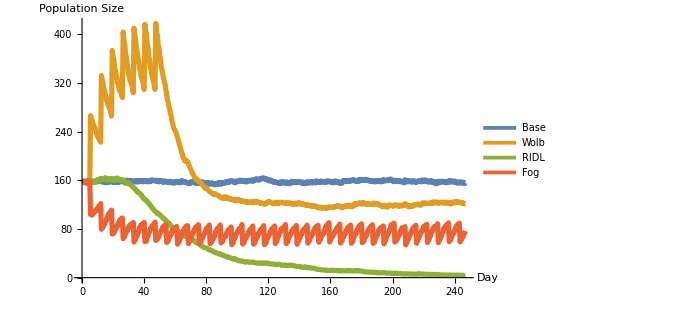
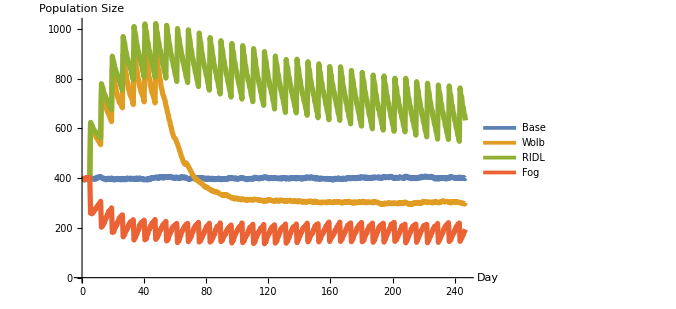
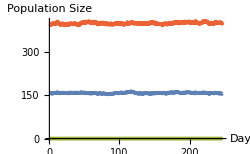
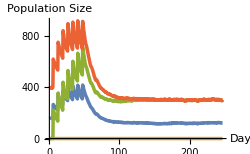
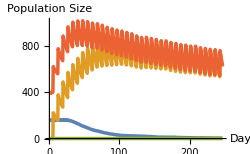
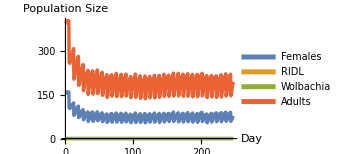
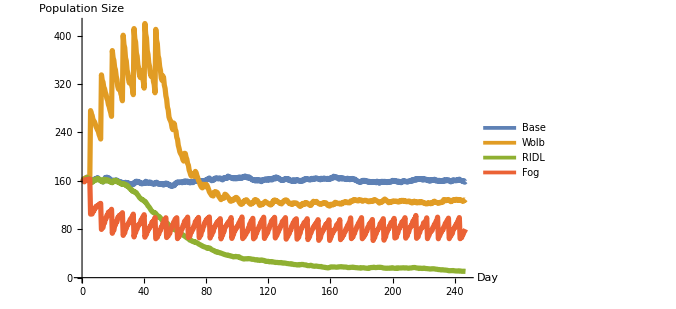
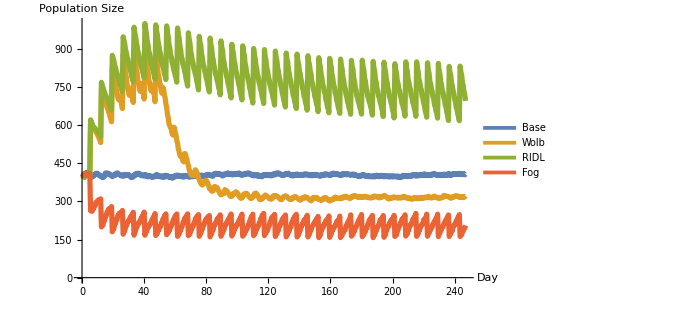
{-Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-}

```mathematica
DynamicsPlotsGrids=Grid[{
{Grid[{#[[1]]}]},
{Grid[{{#[[2,1,1]],#[[2,2,1]],#[[2,3,1]],#[[2,4]]}}]}
}]&/@{HOMDynamicsPlots,HETDynamicsPlots}
```

## Repetition List Plots

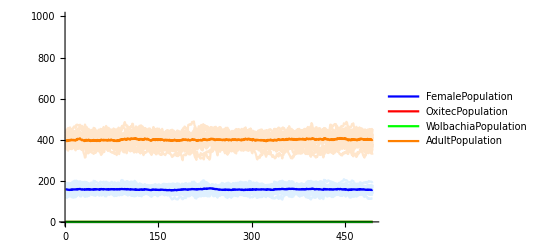
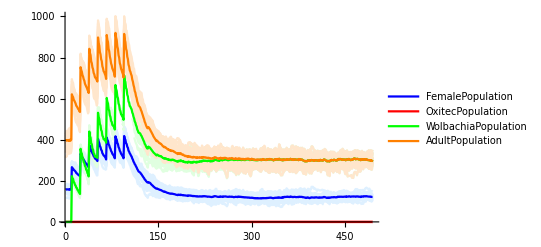
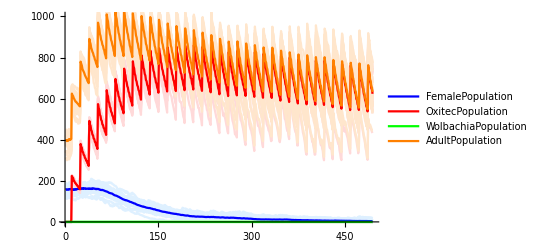
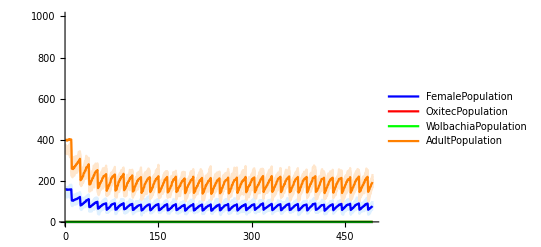
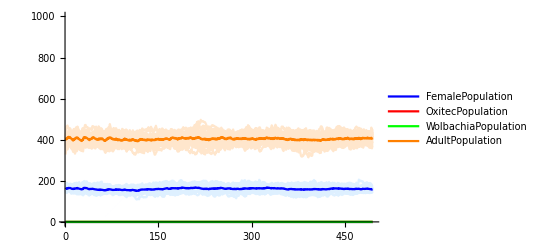
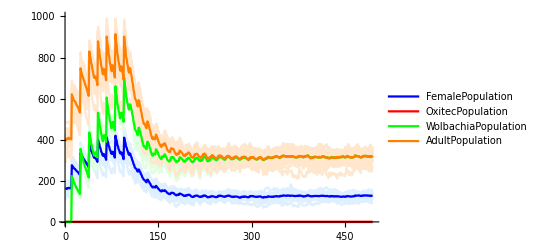
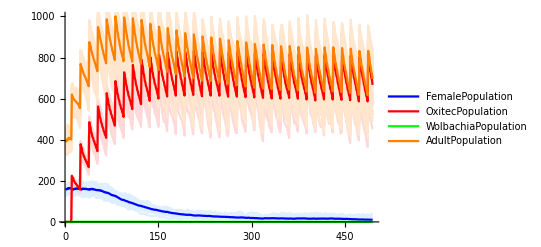
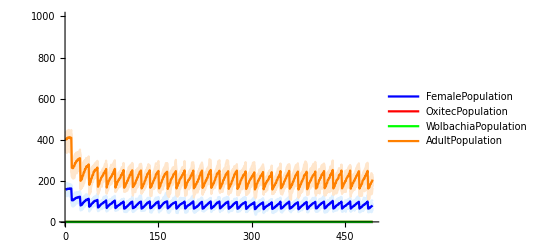
{-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-}

```mathematica
HOMRepetitionsListPlots=ListPlotRepetitions[HOMDataRaw,1000];
HETRepetitionsListPlots=ListPlotRepetitions[HETDataRaw,1000];
DynamicsRepetitionsPlotsGrids={Grid[Partition[HOMRepetitionsListPlots,2]],Grid[Partition[HETRepetitionsListPlots,2]]}
```

## AUC

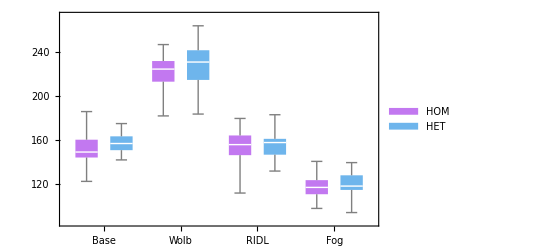

```mathematica
femalesAUCRepetitions={RepetitionsFemalesAUCPerDay[HOMDataRaw],RepetitionsFemalesAUCPerDay[HETDataRaw]};
HOMAUC=BoxWhiskerChart[femalesAUCRepetitions//Transpose,ChartLabels->{(Rotate[Style[#,15],90Degree]&/@labels),None},ChartStyle->"Pastel",ChartLegends->{"HOM","HET"}]
```

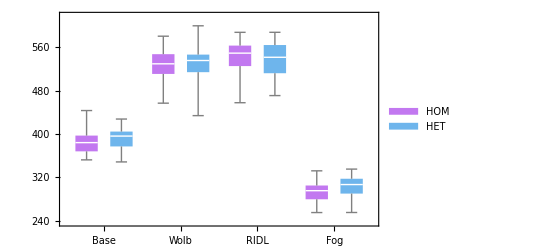

```mathematica
adultsAUCRepetitions={RepetitionsAdultsAUCPerDay[HOMDataRaw],RepetitionsAdultsAUCPerDay[HETDataRaw]};
HETAUC=BoxWhiskerChart[adultsAUCRepetitions//Transpose,ChartLabels->{(Rotate[Style[#,15],90Degree]&/@labels),None},ChartStyle->"Pastel",ChartLegends->{"HOM","HET"}]
```

## 3. Networks

## Calculate Networks

```mathematica
(*Matrices*)
HOMBitesMatrices=ParallelMap[GetExperimentTransitionsMatrices,HOMPaths];
HETBitesMatrices=ParallelMap[GetExperimentTransitionsMatrices,HETPaths];
(*Networks*)
HOMNetworks=ParallelMap[GetNetworks,HOMBitesMatrices];
HETNetworks=ParallelMap[GetNetworks,HETBitesMatrices];
(*Network Measures*)
HOMMeasures=ParallelMap[GetNetworkMeasures,HOMNetworks];
HETMeasures=ParallelMap[GetNetworkMeasures,HETNetworks];
(*Network Communities*)
HOMNetworksCommunities=ParallelMap[GetCommunitiesNetworks,HOMNetworks];
HETNetworksCommunities=ParallelMap[GetCommunitiesNetworks,HETNetworks];
(*Network Centrality*)
HOMCentrality=GetCentralityNetworks[#,ClosenessCentrality]&/@HOMNetworks;
HETCentrality=GetCentralityNetworks[#,ClosenessCentrality]&/@HETNetworks;
```

```mathematica
colorScale=GridColorScaleFrequency[10,10,{{minEdges,maxEdges}}]
```

Frequency | 5. | 6. | 7. | 8. | 9. | 10. | 11. | 12. | 13. | 14. | 15.
Color | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
HOMNetworks[[All,1,2]];
HETNetworks[[All,1,2]];
```

## Centrality

```mathematica
HOMCentrality[[1]][[1,1]]
HETCentrality[[1]][[1,1]]
```

-Graphics-

-Graphics-

## BoxWhiskerCharts

### Individual

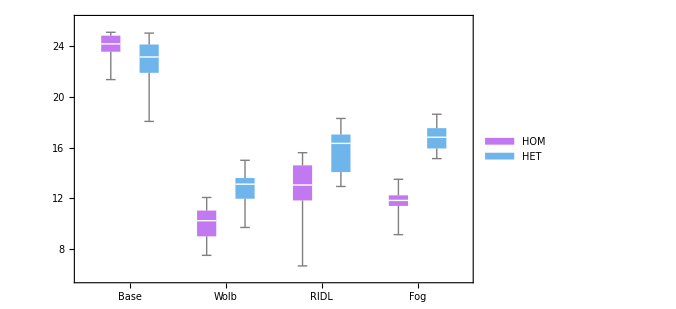
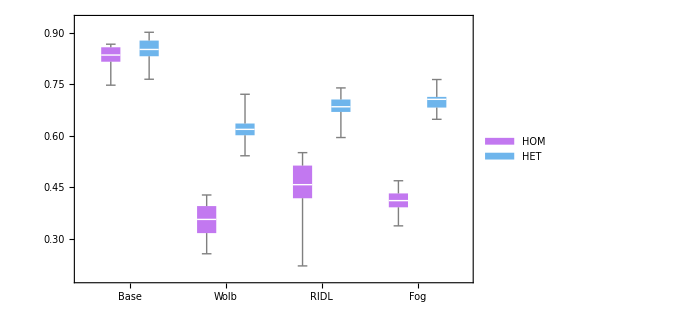
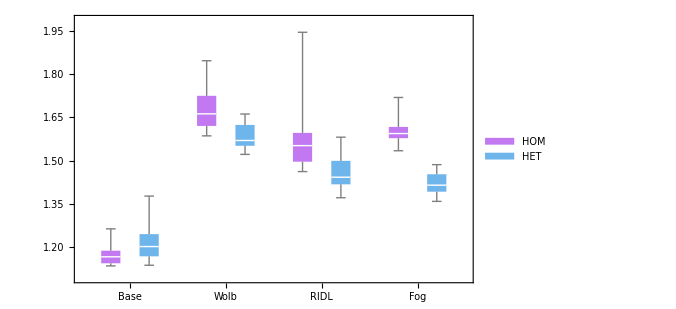
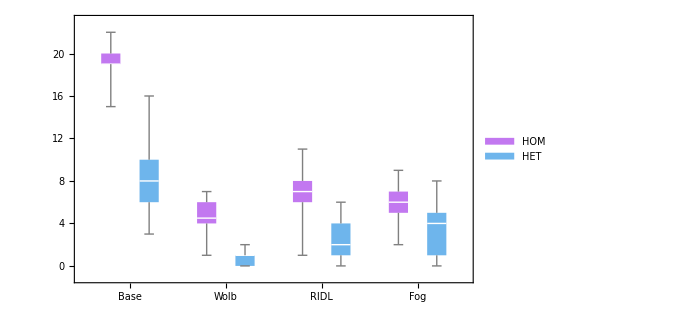
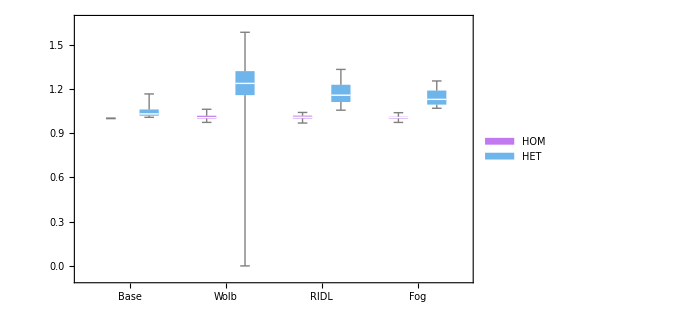
{Mean[VertexInDegree[#1]] & 
-Graphics-,GlobalClusteringCoefficient
-Graphics-,MeanGraphDistance
-Graphics-,EdgeConnectivity
-Graphics-,GetSmallWorldCoefficient[#1, 500] & 
-Graphics-}

```mathematica
j=2;
boxWhiskerCharts=Table[
a={(HOMMeasures[[All,2,j]]//Transpose)[[i]],(HETMeasures[[All,2,j]]//Transpose)[[i]]}//Transpose;
(*b=Mean[Map[Mean,a,2]];
c=a/If[b==∞,1,b];*)
Grid[{
{Style[ToString[measures[[i]]](*<>" * "<>ToString[b]*),25]},
{
BoxWhiskerChart[a,
ChartLegends->{"HOM","HET"},
(*GridLines->{Range[0,100,2+(labels//Length)*2],Range[0,100,.5]},*)
BarSpacing->1,
ChartStyle->"Pastel",
ImageSize->500,
(*PlotRange->{0,All},*)
Method->{"BoxWidth"->"Fixed"},
ChartLabels->{Style[#,20]&/@Flatten[ConstantArray[labels,measures//Length]],None}
]
}
}]
,{i,1,measures//Length}]
```

### Full

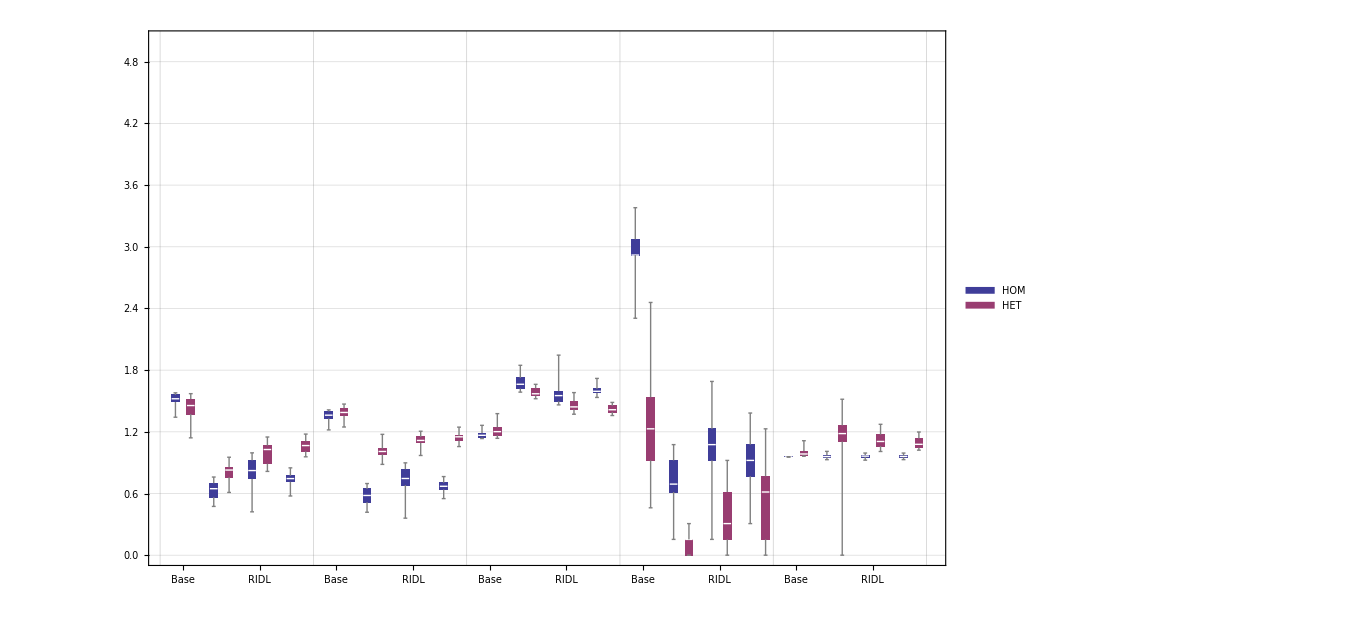

```mathematica
j=1;
Table[
a={(HOMMeasures[[All,2,j]]//Transpose)[[i]],(HETMeasures[[All,2,j]]//Transpose)[[i]]}//Transpose;
b=Mean[Map[Mean,a,2]];
a/If[b==∞,1,b]
,{i,1,measures//Length}];
BoxWhiskerChart[Flatten[%,1],
ChartLegends->{"HOM","HET"},
GridLines->{Range[0,100,2+(labels//Length)*2],Range[0,100,.5]},
BarSpacing->1,
ChartStyle->1,
ImageSize->1000,
PlotRange->{0,5},
Method->{"BoxWidth"->"Fixed"},
ChartLabels->{Flatten[ConstantArray[labels,measures//Length]],None}
]
```

## Degree Distribution

### Repetitions Histograms

```mathematica
(*Histogram*)
HOMHistograms=ParallelMap[PlotHistogramsSet[#,{{0,35},{0,30}}]&,HOMNetworks];
HETHistograms=ParallelMap[PlotHistogramsSet[#,{{0,35},{0,30}}]&,HETNetworks];
(*Smooth Histograms*)
HOMSmoothHistograms=ParallelMap[PlotSmoothHistogramsSet[#,{{0,35},{0,.5}}]&,HOMNetworks];
HETSmoothHistograms=ParallelMap[PlotSmoothHistogramsSet[#,{{0,35},{0,.5}}]&,HETNetworks];
```

```mathematica
HOMHistogramGrid=Grid[Prepend[HOMHistograms//Transpose,labels]];
HETHistogramGrid=Grid[Prepend[HETHistograms//Transpose,labels]];

HOMSmoothHistogramGrid=Grid[Prepend[HOMSmoothHistograms//Transpose,labels]];
HETSmoothHistogramGrid=Grid[Prepend[HETSmoothHistograms//Transpose,labels]];
```

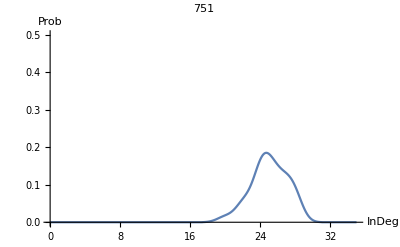
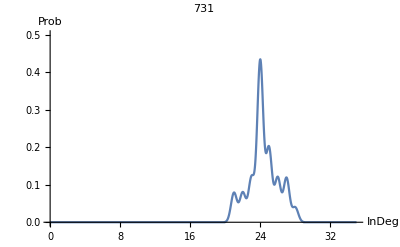
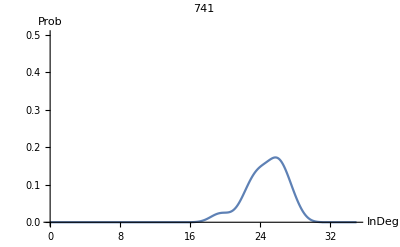
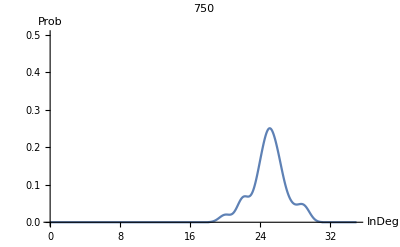
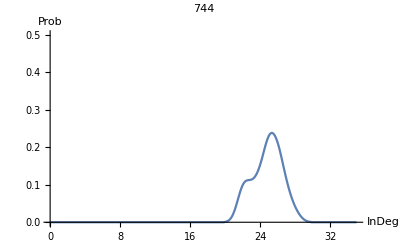
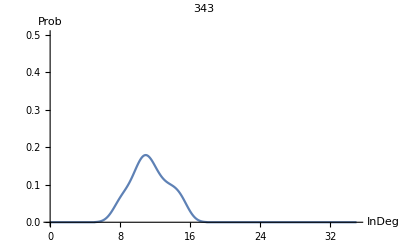
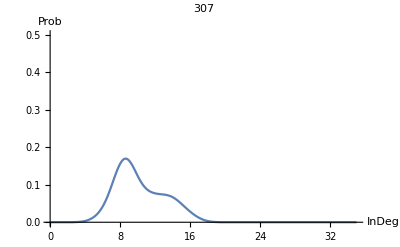
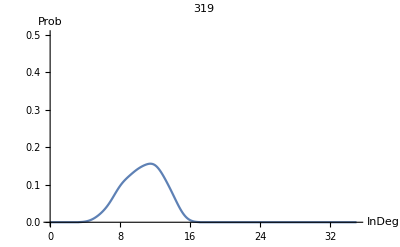
Base | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Wolb | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
RIDL | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Fog | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

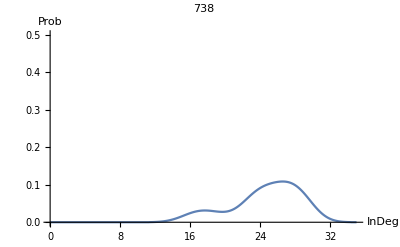
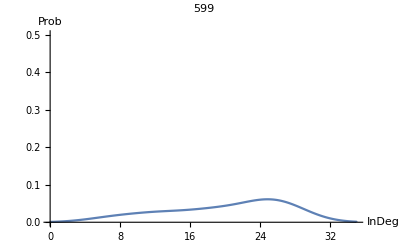
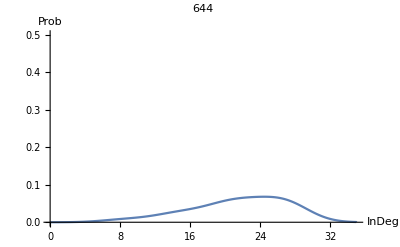
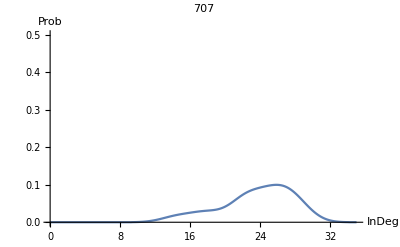
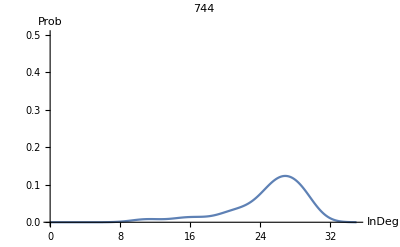
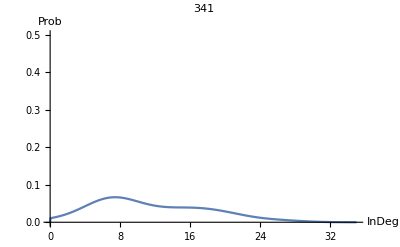
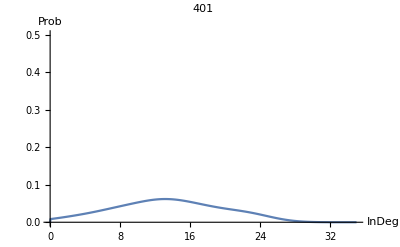
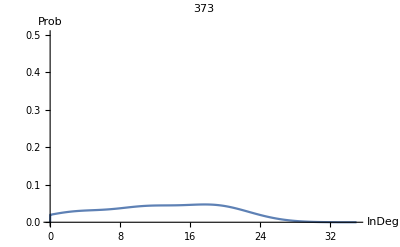
Base | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Wolb | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
RIDL | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Fog | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Prepend[HOMSmoothHistograms[[All,1;;5]]//Transpose,labels]//Transpose]
Grid[Prepend[HETSmoothHistograms[[All,1;;5]]//Transpose,labels]//Transpose]
```

### Mean Histograms

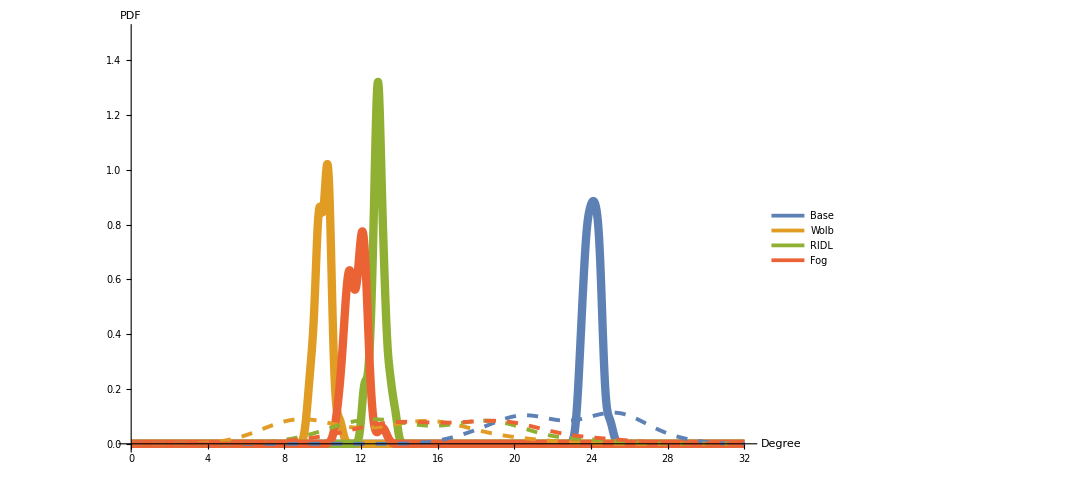
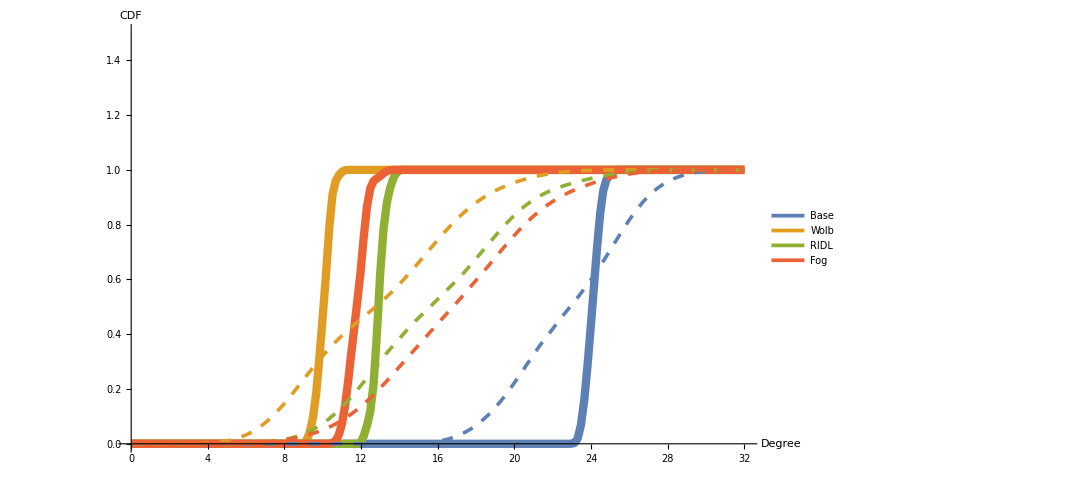
-Graphics- | -Graphics-

```mathematica
(*PDF*)
HOMMeanSmooth=SmoothHistogram[Table[Mean/@((VertexInDegree[#]&/@HOMNetworks[[i]][[2,2]])//Transpose)//N,{i,1,HOMNetworks//Length}],
Automatic,"PDF",
PlotRange->{{0,32},{0,1.5}},
PlotStyle->Thickness[.0075],
TicksStyle->Directive[Black,25],
LabelStyle->Directive[Black,25],
PlotLegends->labels
];
HETMeanSmooth=SmoothHistogram[Table[Mean/@((VertexInDegree[#]&/@HETNetworks[[i]][[2,2]])//Transpose)//N,{i,1,HOMNetworks//Length}],Automatic,"PDF",
PlotRange->{{0,32},{0,1.25}},
PlotStyle->ConstantArray[{Dashing[.01],Thickness[.0035]},labels//Length],
TicksStyle->Directive[Black,25],
LabelStyle->Directive[Black,25]
];
MeanSmoothsPDF=Show[{HOMMeanSmooth,HETMeanSmooth},AxesLabel->{"Degree","PDF"},ImageSize->800];
(*CDF*)
HOMMeanSmoothCDF=SmoothHistogram[Table[Mean/@((VertexInDegree[#]&/@HOMNetworks[[i]][[2,2]])//Transpose)//N,{i,1,HOMNetworks//Length}],
Automatic,"CDF",
PlotRange->{{0,32},{0,1.5}},
PlotLegends->labels,
PlotStyle->Thickness[.0075],
TicksStyle->Directive[Black,25],
LabelStyle->Directive[Black,25]
];
HETMeanSmoothCDF=SmoothHistogram[Table[Mean/@((VertexInDegree[#]&/@HETNetworks[[i]][[2,2]])//Transpose)//N,{i,1,HOMNetworks//Length}],Automatic,"CDF",
PlotRange->{{0,32},{0,1.25}},
PlotStyle->ConstantArray[{Dashing[.01],Thickness[.00325]},labels//Length],
TicksStyle->Directive[Black,25],
LabelStyle->Directive[Black,25]
];
MeanSmoothsCDF=Show[{HOMMeanSmoothCDF,HETMeanSmoothCDF},AxesLabel->{"Degree","CDF"},ImageSize->800];
(*PDF+CDF*)
MeanSmoothsGrid=Grid[{{MeanSmoothsPDF,MeanSmoothsCDF}}]
(*Intensity*)
(*HOMMeanSmooth=SmoothHistogram[Table[
Mean/@((VertexInDegree[#]&/@HOMNetworks[[i]][[2,2]])//Transpose)//N
,{i,1,HOMNetworks//Length}],Automatic,"Intensity",PlotLegends->labels,PlotStyle->Thickness[.0075],PlotRange->{{0,32},{0,1250}}];
HETMeanSmooth=SmoothHistogram[Table[
Mean/@((VertexInDegree[#]&/@HETNetworks[[i]][[2,2]])//Transpose)//N
,{i,1,HOMNetworks//Length}],Automatic,"Intensity",PlotStyle->ConstantArray[{Dashing[1],Thickness[.0025]},labels//Length],PlotRange->{{0,35},{0,1250}}];
MeanSmoothsPDF=Show[{HOMMeanSmooth,HETMeanSmooth},AxesLabel->{"Degree","Probability"},ImageSize->800];*)
```

```mathematica
bins=5;
Table[
ListPlot[Tally[Median/@((VertexInDegree[#]&/@HOMNetworks[[i]][[2,2]])//Transpose)//N],PlotRange->{{0,30},{0,10}}]
,{i,1,HOMNetworks//Length}];
Table[
ListPlot[Tally[Median/@((VertexInDegree[#]&/@HETNetworks[[i]][[2,2]])//Transpose)//N],PlotRange->{{0,30},{0,10}}]
,{i,1,HOMNetworks//Length}];
```

## Mean Matrix Plots

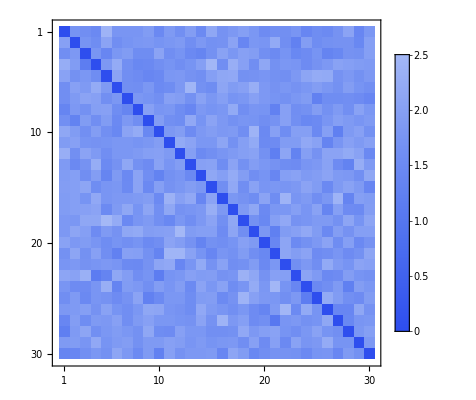
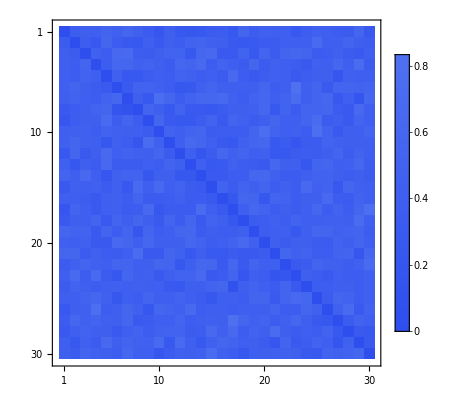
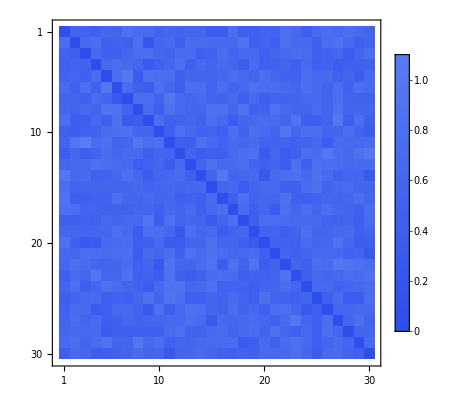
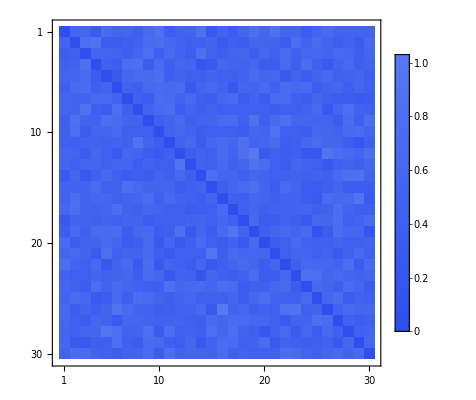

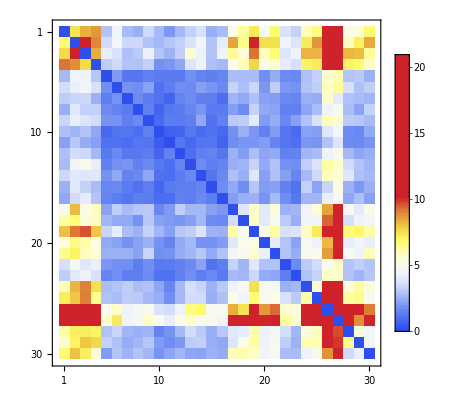
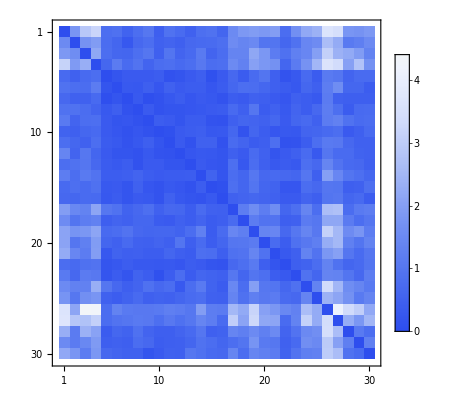
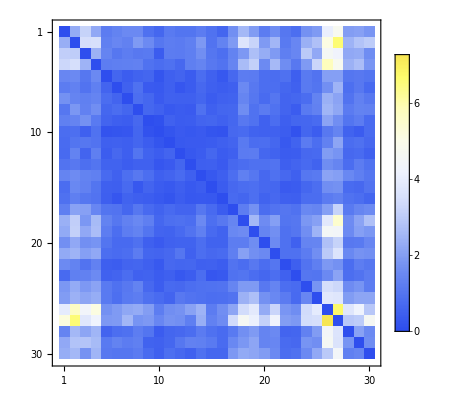
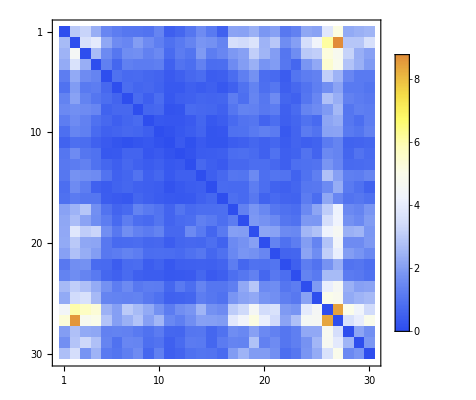

```mathematica
HOMMeanMatrixPlots=ParallelTable[i[[1,2,1]]//MatrixPlot[#,PlotLegends->Automatic,
ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,10}]]&),ColorFunctionScaling->False]&,{i,HOMBitesMatrices}]
HETMeanMatrixPlots=ParallelTable[i[[1,2,1]]//MatrixPlot[#,ColorFunctionScaling->False,PlotLegends->Automatic,
ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{0,10}]]&),ColorFunctionScaling->False]&,{i,HETBitesMatrices}]
HOMNetworks[[All,1,2]];
HETNetworks[[All,1,2]];
```

## FullMatrixPlots

```mathematica
j=2;
HOMFullMatricesPlots=Table[
ParallelMap[MatrixPlot,HOMBitesMatrices[[i]][[2,j,1]]]
,{i,1,HOMBitesMatrices//Length}];
HETFullMatricesPlots=Table[
ParallelMap[MatrixPlot,HETBitesMatrices[[i]][[2,j,1]]]
,{i,1,HOMBitesMatrices//Length}];
```

## 4. ANOVA

## CI

```mathematica
HOMCIs=GetCIs/@HOMMeasures;
HETCIs=GetCIs/@HETMeasures;
HOMCIPlots=GetCIPlots[HOMCIs];
HETCIPlots=GetCIPlots[HETCIs];

j=2;
HOMCIGrid=Grid[{measures,HOMCIPlots[[j]]}//Transpose];
HETCIGrid=Grid[{measures,HETCIPlots[[j]]}//Transpose];
```

## Effect Size

```mathematica
HOMCohen=GetCohen[HOMMeasures]
HETCohen=GetCohen[HETMeasures]
HOMCohenR=GetCohenR[HOMMeasures]
HETCohenR=GetCohenR[HETMeasures]
```

{{{0.,12.7011,6.77543,13.2771},{0.,12.1781,6.65728,13.2898},{0.,9.52965,5.43219,12.3043},{0.,10.8857,7.03534,10.151},{0.,0.62041854542236,0.701268522106799,0.601303629320019}},{{0.,12.8531,6.82998,13.2685},{0.,12.1781,6.65728,13.2898},{0.,9.52965,5.43219,12.3043},{0.,10.8857,7.03534,10.151},{0.,0.633090008203841,0.699631317362701,0.611142793588339}}}

{{{0.,6.77471,4.22399,4.25258},{0.,5.8621,4.83431,4.96381},{0.,0.983193,0.695223,0.621826},{0.,3.10159,2.1673,1.64559},{0.,0.136696343642282,2.16769778314445,2.05922843489576}},{{0.,6.81522,4.19755,4.28448},{0.,5.8621,4.83431,4.96381},{0.,0.983193,0.695223,0.621826},{0.,3.10159,2.1673,1.64559},{0.,0.135957646051456,2.16981577085549,2.06160430779427}}}

{{{6.10855×10^-177,0.43241,0.762265,0.199651},{1.,0.681096,0.813068,0.095461},{1.,0.393551,0.804398,0.220542},{5.97647×10^-193,0.089478,0.422176,0.577414},{1.,0.0160185,0.288566,0.0271508}},{{2.74239×10^-173,0.474173,0.752707,0.169066},{1.,0.681096,0.813068,0.095461},{1.,0.393551,0.804398,0.220542},{5.97647×10^-193,0.089478,0.422176,0.577414},{9.73833×10^-132,0.0261242,0.28806,0.0198854}}}

{{{1.,0.225047,0.0275429,0.129653},{1.,0.269479,0.225687,0.646323},{1.,0.167508,0.766976,0.53004},{5.06227×10^-214,0.0107071,0.460723,0.962972},{7.20468×10^-187,0.12903,0.130474,0.0843166}},{{1.,0.211829,0.0232027,0.101034},{1.,0.269479,0.225687,0.646323},{1.,0.167508,0.766976,0.53004},{5.06227×10^-214,0.0107071,0.460723,0.962972},{1.,0.12883,0.137775,0.0851851}}}

## ANOVA

```mathematica
HOMAnova=GetANOVA[HOMMeasures];
HETAnova=GetANOVA[HETMeasures];
```

## Grids

### Effect Size

```mathematica
j=2;

tables=Table[
{
Grid[{labels,NumberForm[#,4]&/@HOMCohen[[j]][[k]],NumberForm[#,4]&/@HOMCohenR[[j]][[k]]}//Transpose//Prepend[#,{"","d","r"}]&,Background->{{LightBlue},{LightBlue}},ItemSize->8],
Grid[{labels,NumberForm[#,4]&/@HETCohen[[j]][[k]],NumberForm[#,4]&/@HETCohenR[[j]][[k]]}//Transpose//Prepend[#,{"","d","r"}]&,Background->{{LightBlue},{LightBlue}},ItemSize->8]
}
,{k,1,measures//Length}];
```

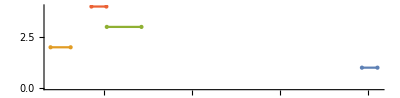
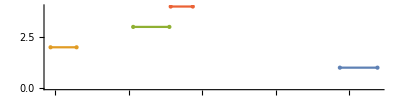
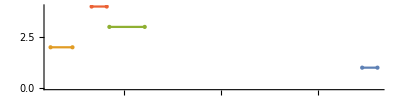
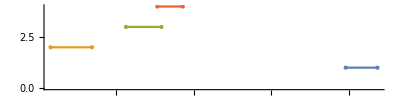
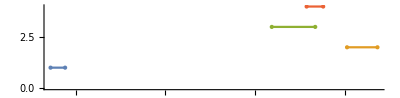
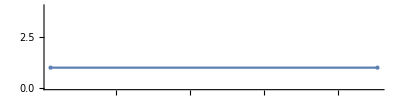
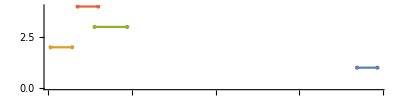
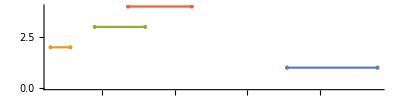
Measure | HOM | HET
Mean[VertexInDegree[#1]]& | -Graphics- |  | d | r
Base | 0. | 2.742×10^-173
Wolb | 12.85 | 0.4742
RIDL | 6.83 | 0.7527
Fog | 13.27 | 0.1691 | -Graphics- |  | d | r
Base | 0. | 1.
Wolb | 6.815 | 0.2118
RIDL | 4.198 | 0.0232
Fog | 4.284 | 0.101
GlobalClusteringCoefficient | -Graphics- |  | d | r
Base | 0. | 1.
Wolb | 12.18 | 0.6811
RIDL | 6.657 | 0.8131
Fog | 13.29 | 0.09546 | -Graphics- |  | d | r
Base | 0. | 1.
Wolb | 5.862 | 0.2695
RIDL | 4.834 | 0.2257
Fog | 4.964 | 0.6463
MeanGraphDistance | -Graphics- |  | d | r
Base | 0. | 1.
Wolb | 9.53 | 0.3936
RIDL | 5.432 | 0.8044
Fog | 12.3 | 0.2205 | -Graphics- |  | d | r
Base | 0. | 1.
Wolb | 0.9832 | 0.1675
RIDL | 0.6952 | 0.767
Fog | 0.6218 | 0.53
EdgeConnectivity | -Graphics- |  | d | r
Base | 0. | 5.976×10^-193
Wolb | 10.89 | 0.08948
RIDL | 7.035 | 0.4222
Fog | 10.15 | 0.5774 | -Graphics- |  | d | r
Base | 0. | 5.062×10^-214
Wolb | 3.102 | 0.01071
RIDL | 2.167 | 0.4607
Fog | 1.646 | 0.963
GetSmallWorldCoefficient[#1,500]& | -Graphics- |  | d | r
Base | 0. | 9.738×10^-132
Wolb | 0.6331 | 0.02612
RIDL | 0.6996 | 0.2881
Fog | 0.6111 | 0.01989 | -Graphics- |  | d | r
Base | 0. | 1.
Wolb | 0.1360 | 0.1288
RIDL | 2.170 | 0.1378
Fog | 2.062 | 0.08519

```mathematica
effectSizeGrid=Grid[
Prepend[{
measures,
Grid[{#}]&/@({HOMCIPlots[[j]],tables[[All,1]]}//Transpose),
Grid[{#}]&/@({HETCIPlots[[j]],tables[[All,2]]}//Transpose)
}//Transpose,{"Measure","HOM","HET"}],
Frame->All,
Background->{{LightPurple},{LightPurple}}]
```

### ANOVA

```mathematica
j=1;
(**)
pValues=HOMAnova[[j]][[All,1,2,1,1,5]];
tukeys=HOMAnova[[j]][[All,3,2,1,2,1,1,2]];
```

```mathematica
HOMAnova[[1]];
```

```mathematica
tups=Tuples[labels,2]

orTuks=tukeys[[6]];
revTuks=Reverse/@tukeys[[1]];
fullTuks=Flatten[{orTuks,revTuks},1]
ReplaceAll[tups,#[[1]]->#[[2]]&/@({fullTuks,ConstantArray["T",fullTuks//Length]}//Transpose)]
```

{{Base,Base},{Base,Wolb},{Base,RIDL},{Base,Fog},{Wolb,Base},{Wolb,Wolb},{Wolb,RIDL},{Wolb,Fog},{RIDL,Base},{RIDL,Wolb},{RIDL,RIDL},{RIDL,Fog},{Fog,Base},{Fog,Wolb},{Fog,RIDL},{Fog,Fog}}

Part::partw: Part 6 of {{{Base,Fog},{Base,RIDL},{Fog,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{{Base,Fog},{Base,RIDL},{Fog,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{{Base,Fog},{Base,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{{Base,Fog},{Base,RIDL},{Fog,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{}} does not exist.

{{{{Base,Fog},{Base,RIDL},{Fog,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{{Base,Fog},{Base,RIDL},{Fog,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{{Base,Fog},{Base,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{{Base,Fog},{Base,RIDL},{Fog,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{}}⟦6⟧,{Fog,Base},{RIDL,Base},{RIDL,Fog},{Wolb,Base},{Wolb,Fog},{Wolb,RIDL}}

Part::partw: Part 6 of {{{Base,Fog},{Base,RIDL},{Fog,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{{Base,Fog},{Base,RIDL},{Fog,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{{Base,Fog},{Base,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{{Base,Fog},{Base,RIDL},{Fog,RIDL},{Base,Wolb},{Fog,Wolb},{RIDL,Wolb}},{}} does not exist.

{{Base,Base},{Base,Wolb},{Base,RIDL},{Base,Fog},T,{Wolb,Wolb},T,T,T,{RIDL,Wolb},{RIDL,RIDL},T,T,{Fog,Wolb},{Fog,RIDL},{Fog,Fog}}

## 5. Repetitions Summary

```mathematica
HOMSummaries=GetSummaries[HOMMeasures];
HETSummaries=GetSummaries[HETMeasures];
j=2;
Grid[{{HOMSummaries[[2,j]],HETSummaries[[2,j]]}}]
```

Measure | Mean[VertexInDegree[#1]]& | GlobalClusteringCoefficient | MeanGraphDistance | EdgeConnectivity | GetSmallWorldCoefficient[#1,500]&
Base | 25.9667 | 0.864012 | 1.13678 | 20. | 13173268750/13175604907
Base | 25.1333 | 0.841778 | 1.15977 | 19. | 12960234672000/12959831097139
Base | 25.5667 | 0.853947 | 1.14828 | 19. | 119818668475/119798763324
Base | 25.9333 | 0.862231 | 1.13793 | 20. | 105144550000/105160278971
Base | 25.7 | 0.857816 | 1.14483 | 21. | 2413161495000/2412957812651
Base | 23.7667 | 0.791028 | 1.20575 | 18. | 8675750512000/8682042162081
Base | 25.4333 | 0.849847 | 1.14943 | 20. | 2368428174000/2367724374697
Base | 22.0667 | 0.747409 | 1.26322 | 17. | 239693065937000/239179118657461
Base | 25.4 | 0.848662 | 1.15287 | 18. | 1198026622000/1198109900513
Base | 23.2667 | 0.782266 | 1.21954 | 18. | 12751917851750/12742910738249
Base | 24.9333 | 0.831388 | 1.17011 | 19. | 400143075000/400281634729
Base | 24.5 | 0.815763 | 1.18736 | 19. | 6498276980250/6495883181171
Base | 25.9333 | 0.863644 | 1.13563 | 20. | 104944202000/104914382283
Base | 24.9667 | 0.830432 | 1.16897 | 20. | 2005962365000/2003513185741
Base | 23.1333 | 0.77103 | 1.23103 | 18. | 19216145072740/19228431146807
Base | 25.4 | 0.84746 | 1.15402 | 20. | 13233835450000/13240570932671
Base | 25.8667 | 0.866227 | 1.13563 | 22. | 4341736795000/4341051660021
Base | 24.6 | 0.818717 | 1.18161 | 19. | 1732417500000/1732269159301
Base | 24.9333 | 0.832165 | 1.16897 | 19. | 4334589671500/4341150782589
Base | 25.8333 | 0.860308 | 1.14023 | 21. | 10414786600/10417776093
Base | 24.4 | 0.810887 | 1.18851 | 19. | 25772695712500/25795705956181
Base | 23.5333 | 0.782994 | 1.21839 | 15. | 25359007822500/25361991791203
Base | 25.6333 | 0.859151 | 1.14253 | 20. | 2401796344000/2401724355607
Base | 25.0667 | 0.834021 | 1.16552 | 19. | 518565649800/518433868049
Base | 24.6 | 0.822692 | 1.17701 | 19. | 13094171860000/13084224591859
Base | 25.9 | 0.866816 | 1.13448 | 20. | 7529000000/7528966857
Base | 24.8333 | 0.82928 | 1.17126 | 20. | 57158030050/57159153669
Base | 24.9667 | 0.836419 | 1.16667 | 20. | 26230731087000/26232479961217
Base | 25.6333 | 0.856831 | 1.14368 | 19. | 480274960000/480342462147
Base | 23.9667 | 0.795354 | 1.2046 | 19. | 1620937951875/1620158360606
Wolb | 11.9 | 0.404984 | 1.6092 | 6. | 31504748226250/31274936116509
Wolb | 10.6 | 0.361481 | 1.65517 | 6. | 59944276675000/59767133562601
Wolb | 10.9 | 0.356227 | 1.63908 | 6. | 118355717940000/118618835737469
Wolb | 9.33333 | 0.309379 | 1.72414 | 3. | 13921175115457135/13800726262486303
Wolb | 11.0667 | 0.369512 | 1.64713 | 5. | 124300953897500/119431485455421
Wolb | 11.7 | 0.408169 | 1.61264 | 7. | 77000917303500/76176278371199
Wolb | 11.6667 | 0.395118 | 1.61494 | 6. | 387942297454500/380413686471319
Wolb | 10.8 | 0.365534 | 1.65747 | 6. | 35841999354228275/36313449134377139
Wolb | 9.93333 | 0.336489 | 1.68161 | 4. | 176218505996250/170145861465563
Wolb | 9.26667 | 0.29355 | 1.74253 | 4. | 17166942601812005/17076517180238351
Wolb | 9. | 0.277092 | 1.74138 | 4. | 13344512744986365/13328790202416592
Wolb | 10.0333 | 0.347413 | 1.67356 | 4. | 7058845835853030/7056193689180031
Wolb | 9.43333 | 0.325534 | 1.7092 | 5. | 5596739531681350/5639768619232999
Wolb | 11.3333 | 0.371958 | 1.62989 | 5. | 365816834250000/373936115173283
Wolb | 11. | 0.347309 | 1.64138 | 5. | 58444994330000/59316148370337
Wolb | 9.23333 | 0.32956 | 1.72529 | 1. | 301304681117611/292171530311318
Wolb | 10.6667 | 0.371917 | 1.66782 | 4. | 24247109864000/23366594285433
Wolb | 11.7 | 0.407505 | 1.61264 | 6. | 381234998404500/376686632838139
Wolb | 7.8 | 0.298392 | 1.84598 | 3. | 12794712917019878/12062235402394461
Wolb | 7.9 | 0.256184 | 1.84713 | 2. | 93764152247398/94154907842957
Wolb | 12. | 0.415601 | 1.61264 | 5. | 47645397343125/47271806111987
Wolb | 11.3333 | 0.361498 | 1.62529 | 6. | 182777468205000/184047270322493
Wolb | 9.13333 | 0.316411 | 1.73563 | 4. | 5541430306413365/5527220476120164
Wolb | 12.0667 | 0.411721 | 1.6046 | 4. | 48317953543875/47585754884501
Wolb | 8.8 | 0.31136 | 1.76782 | 4. | 6594735845912672/6435025601148053
Wolb | 9.83333 | 0.328319 | 1.7069 | 4. | 4639835414530239/4615326845494381
Wolb | 11.5 | 0.41121 | 1.62069 | 5. | 18605465125125/18580535946746
Wolb | 12.5 | 0.427459 | 1.58621 | 7. | 98554591498125/98290498911709
Wolb | 10.1667 | 0.356415 | 1.68851 | 4. | 4733258623319239/4659997630830696
Wolb | 8.86667 | 0.294991 | 1.73333 | 4. | 64754391371606145/66538584479894314
RIDL | 11.7667 | 0.394281 | 1.61149 | 6. | 23020770600000/22585996232923
RIDL | 13.5667 | 0.448213 | 1.55172 | 7. | 34419776701875/34151423154044
RIDL | 12.5667 | 0.424922 | 1.57356 | 8. | 3562449410000/3617598480463
RIDL | 15.5333 | 0.523751 | 1.48391 | 10. | 13366818717237000/13371003524893397
RIDL | 12.8333 | 0.448127 | 1.57011 | 7. | 213521136915750/209142968554409
RIDL | 11.2333 | 0.386593 | 1.62874 | 6. | 43762437146642445/44493897324662708
RIDL | 15.7667 | 0.531921 | 1.47471 | 9. | 6715310232243500/6724633476920487
RIDL | 15.0333 | 0.513139 | 1.4977 | 8. | 6573649359733750/6485472372776711
RIDL | 15.6667 | 0.515376 | 1.48046 | 11. | 13358009324017000/13331206978114681
RIDL | 14.1 | 0.478228 | 1.53448 | 5. | 48591946842500/47393681759109
RIDL | 6.93333 | 0.220818 | 1.94598 | 1. | 81664852614970/81827149204309
RIDL | 13.5333 | 0.45336 | 1.55287 | 7. | 52576280044875/52100101966007
RIDL | 14.4 | 0.488826 | 1.52184 | 7. | 224818117079250/222299132721677
RIDL | 13.4 | 0.449413 | 1.55517 | 7. | 11987254993659000/11930568518505431
RIDL | 16.0333 | 0.537964 | 1.46782 | 6. | 4537233650736000/4485459970387441
RIDL | 12.2 | 0.430951 | 1.59655 | 6. | 199132285401000/194464068736249
RIDL | 15.7333 | 0.538427 | 1.48046 | 10. | 13303666981787000/13215306511833477
RIDL | 11.0333 | 0.393701 | 1.64138 | 3. | 14631104419719321/14400857400861317
RIDL | 14.3 | 0.46894 | 1.52874 | 7. | 433317028482000/434718246119981
RIDL | 16.3667 | 0.550847 | 1.46207 | 10. | 122567976959625/121529669832214
RIDL | 13.0667 | 0.46173 | 1.55977 | 6. | 443231599500/434960867329
RIDL | 12.7667 | 0.417978 | 1.57471 | 8. | 33836063917500/34040832611599
RIDL | 14.7667 | 0.50987 | 1.50575 | 9. | 2155167790561000/2141576967524673
RIDL | 9.23333 | 0.345269 | 1.72414 | 5. | 11693932624473310/11293445864811233
RIDL | 13.5333 | 0.47446 | 1.54713 | 7. | 6472302400750/6399736280697
RIDL | 11.9 | 0.419129 | 1.60805 | 6. | 18739591065924095/18803625457251606
RIDL | 15.1667 | 0.503969 | 1.49655 | 8. | 899441965591200/899742790280761
RIDL | 10.2333 | 0.333215 | 1.67471 | 5. | 68583202720492895/70892327225576688
RIDL | 12.5 | 0.412197 | 1.5931 | 7. | 200987756484750/197296250520679
RIDL | 15.8 | 0.546284 | 1.47126 | 8. | 13747687511189000/13494171739188933
Fog | 12.3667 | 0.396608 | 1.5954 | 5. | 98399233441125/97630678585646
Fog | 12.7333 | 0.434139 | 1.57816 | 6. | 100691841811125/99667516268219
Fog | 13.3667 | 0.464126 | 1.55862 | 5. | 12231871639467000/12084259485946013
Fog | 11.1667 | 0.37579 | 1.63793 | 7. | 29275842660625/29640405937293
Fog | 11.3667 | 0.393457 | 1.63103 | 6. | 121197497372500/120971215592191
Fog | 12.6 | 0.441197 | 1.58161 | 6. | 34438484432875/34258297634681
Fog | 10.3333 | 0.362693 | 1.67126 | 4. | 104540471824609/103593695446362
Fog | 11.9 | 0.422944 | 1.59885 | 7. | 13095703661900/12602691317177
Fog | 12.0667 | 0.412999 | 1.61724 | 2. | 8406602612043805/8322338785069013
Fog | 13.9667 | 0.465134 | 1.53448 | 9. | 424757023392000/425183440696477
Fog | 12.2667 | 0.402744 | 1.5931 | 6. | 66248617405000/66220410579831
Fog | 12.7 | 0.430928 | 1.57816 | 6. | 404528280960000/399148869382361
Fog | 12.8667 | 0.442399 | 1.57126 | 7. | 205956242831250/200022595477739
Fog | 12.5667 | 0.412235 | 1.5931 | 6. | 389740605429000/384931655484151
Fog | 13.6667 | 0.468967 | 1.54138 | 7. | 35769807470875/35535042333211
Fog | 12.5 | 0.39156 | 1.5931 | 7. | 126596845142500/130086828660977
Fog | 12.3667 | 0.407977 | 1.58736 | 6. | 42811528730000/43257602122533
Fog | 11.0667 | 0.354537 | 1.63793 | 5. | 10148575415946770/10155767234184213
Fog | 11.5667 | 0.38895 | 1.62299 | 5. | 61999438677500/61398337105841
Fog | 11.7333 | 0.390665 | 1.6069 | 6. | 187108922632500/187677910087097
Fog | 12.9 | 0.442468 | 1.57356 | 5. | 409624231087500/402915142240553
Fog | 13.5 | 0.432005 | 1.55287 | 7. | 138033824110000/138958756022019
Fog | 11.8 | 0.404009 | 1.60805 | 6. | 395860054024500/393095220129851
Fog | 12.0667 | 0.422111 | 1.59885 | 7. | 42593633290000/42903165966007
Fog | 11.7667 | 0.386892 | 1.60805 | 6. | 96380485849500/95927469268027
Fog | 11.6333 | 0.393906 | 1.62299 | 6. | 43091957967500/42627534626621
Fog | 12.4667 | 0.421003 | 1.58621 | 6. | 135732395045000/135696682607013
Fog | 12.2 | 0.409892 | 1.59655 | 6. | 897524049712500/899074841770291
Fog | 12.2333 | 0.4125 | 1.5908 | 7. | 376900112647500/374977847496569
Fog | 9.46667 | 0.33753 | 1.71954 | 3. | 69385549846499705/68317647777695646 | Measure | Mean[VertexInDegree[#1]]& | GlobalClusteringCoefficient | MeanGraphDistance | EdgeConnectivity | GetSmallWorldCoefficient[#1,500]&
Base | 25.5 | 0.881268 | 1.15172 | 12. | 19567244331380/19321209464529
Base | 20.7667 | 0.796103 | 1.31149 | 5. | 2212007980241500/2001942688472703
Base | 22.2333 | 0.805411 | 1.25977 | 8. | 1425008779552000/1368880129549429
Base | 24.4667 | 0.857298 | 1.18736 | 10. | 478543532670500/471261701476781
Base | 25.6667 | 0.894391 | 1.14483 | 11. | 24474038032875/24094239404752
Base | 24.9 | 0.877375 | 1.16782 | 10. | 40444285057375/39859089669338
Base | 24.8333 | 0.878802 | 1.17241 | 7. | 8192028122216500/7972150959716759
Base | 21. | 0.814094 | 1.30115 | 4. | 7827776716848250/7007672556339919
Base | 23.2667 | 0.855527 | 1.22529 | 4. | 400658286719325/380485663174834
Base | 18.7667 | 0.764706 | 1.37701 | 3. | 15117964245253500/12973036974447653
Base | 23.0333 | 0.844229 | 1.23333 | 7. | 16087883145188000/15380690484831111
Base | 22.8667 | 0.830456 | 1.23563 | 5. | 322598082368800/309181908595717
Base | 23.9333 | 0.863414 | 1.20345 | 10. | 800909913215250/769035004689859
Base | 20.4333 | 0.789717 | 1.31839 | 6. | 7635083734285000/6906022358353051
Base | 25.2667 | 0.889611 | 1.15632 | 7. | 243872273128750/236802664646119
Base | 22.5667 | 0.828152 | 1.24483 | 7. | 7910515934521000/7447591201524763
Base | 25.5333 | 0.901564 | 1.14713 | 7. | 5188518877200/5072400307963
Base | 24.2667 | 0.85185 | 1.1931 | 13. | 163604300418230/159417182630451
Base | 24.9667 | 0.865553 | 1.17011 | 14. | 24270210726550/23917307907817
Base | 24.0333 | 0.851176 | 1.19885 | 9. | 815846710544650/797207540884483
Base | 25.3667 | 0.873942 | 1.15402 | 14. | 25673032649000/25484414207899
Base | 23.4667 | 0.842467 | 1.21724 | 9. | 476030615039500/461810975788979
Base | 25.8333 | 0.885612 | 1.13678 | 16. | 25866563492000/25672092154811
Base | 25.8333 | 0.889406 | 1.14253 | 12. | 5164676506200/5072162813761
Base | 23.9333 | 0.850326 | 1.2 | 8. | 1011290458147750/983902320578603
Base | 22.3667 | 0.831712 | 1.25287 | 6. | 7949712000312000/7467698247964961
Base | 24.2 | 0.856854 | 1.19425 | 8. | 580390512688125/567968855652089
Base | 23.1333 | 0.848709 | 1.22874 | 4. | 3993112391066375/3765824060882449
Base | 22.4 | 0.833264 | 1.25517 | 6. | 841578267643000/781922983711601
Base | 23.5 | 0.843071 | 1.21609 | 8. | 4036687696025875/3894880221444021
Wolb | 11.8333 | 0.569708 | ∞ | 0. | 0
Wolb | 13.8 | 0.607892 | 1.57471 | 1. | 10211008595481863/8348325344811427
Wolb | 12.9667 | 0.663926 | ∞ | 0. | 0
Wolb | 12.2333 | 0.609491 | 1.64828 | 1. | 95797313422569395/69533042230873537
Wolb | 14.1333 | 0.618841 | 1.54828 | 2. | 280221334513991000/225259036683919601
Wolb | 11.6 | 0.641415 | ∞ | 0. | 0
Wolb | 13.7667 | 0.610592 | 1.56552 | 1. | 232204217650750/190431353174781
Wolb | 14.0667 | 0.599504 | 1.55517 | 1. | 4985521871022750/4216710967260803
Wolb | 14.0667 | 0.599504 | 1.55517 | 1. | 830920311837125/702731089079998
Wolb | 13.6667 | 0.616327 | ∞ | 0. | 0
Wolb | 12. | 0.601507 | 1.65402 | 1. | 72116128351887865/51689856253158504
Wolb | 12.9 | 0.614431 | ∞ | 0. | 141216122498127746/106365572996248125
Wolb | 14.5667 | 0.624067 | 1.55172 | 1. | 68429241676367000/58236025435401849
Wolb | 15.6667 | 0.693497 | ∞ | 0. | 0
Wolb | 13.7667 | 0.635712 | ∞ | 0. | 19201919407814000/14705579650143627
Wolb | 12.4667 | 0.625899 | ∞ | 0. | 0
Wolb | 12.8333 | 0.625418 | 1.64943 | 1. | 37276456424790/29081783745067
Wolb | 14.8 | 0.622111 | 1.52184 | 2. | 468158064590000/404643912352627
Wolb | 11.8333 | 0.559278 | 1.63218 | 2. | 92424460426382711/69941636944192696
Wolb | 15.1333 | 0.715701 | 1.52414 | 1. | 285986125855714/227562908705997
Wolb | 12.1333 | 0.588284 | 1.66207 | 1. | 95047372291318146/69854985272154487
Wolb | 10.0333 | 0.541714 | ∞ | 0. | 5686942847994116/3588371037698205
Wolb | 14.1667 | 0.631227 | 1.55172 | 2. | 9729720251600/7834172793271
Wolb | 12.7667 | 0.594512 | 1.59655 | 2. | 10582601193529013/8098288888018848
Wolb | 13.5667 | 0.607222 | 1.56322 | 2. | 46516154877104500/37698934703908543
Wolb | 14.0667 | 0.720962 | 1.58046 | 1. | 100656547097817500/72331775082255437
Wolb | 14.9 | 0.649874 | 1.54368 | 1. | 47045481633686250/38572615756549597
Wolb | 14.0667 | 0.720962 | 1.58046 | 1. | 1006565470978175/722689638059162
Wolb | 12.6667 | 0.618551 | 1.61609 | 1. | 19193032252976000/14545886412962817
Wolb | 12.6 | 0.63102 | ∞ | 0. | 0
RIDL | 17.5333 | 0.705673 | ∞ | 0. | 1484700333662750/1286145564185511
RIDL | 17.3667 | 0.684489 | 1.42529 | 5. | 7248664837316750/6466831208980703
RIDL | 14.5 | 0.670416 | ∞ | 0. | 482414112182000/370963152943209
RIDL | 14.6333 | 0.66971 | ∞ | 0. | 68982793958901125/57374692997707162
RIDL | 14.6 | 0.594848 | 1.51954 | 2. | 117023486900875/99385937657728
RIDL | 17.7667 | 0.706166 | 1.4092 | 4. | 7285468641724250/6485940485424763
RIDL | 17.9333 | 0.684508 | 1.40345 | 4. | 14793467318937500/14013861046248067
RIDL | 13.7 | 0.613364 | 1.55402 | 3. | 4750370628425/3678229954521
RIDL | 13.7333 | 0.660851 | ∞ | 0. | 86751211240125/69330390826549
RIDL | 14.3333 | 0.628607 | 1.53793 | 3. | 464081014766500/377628826858491
RIDL | 17.5 | 0.673333 | 1.41724 | 6. | 7189147491355000/6563512209600131
RIDL | 14.8333 | 0.670694 | 1.51609 | 2. | 98120363277100/75863491081811
RIDL | 17.5333 | 0.701805 | 1.41954 | 2. | 14038805124180000/12763761630587387
RIDL | 15.8 | 0.694545 | 1.48851 | 1. | 490775242323000/405567606971257
RIDL | 18.8333 | 0.729691 | 1.37356 | 2. | 15082949024826000/13693823081588801
RIDL | 16.3333 | 0.669471 | 1.45977 | 2. | 485854035650000/422472125447031
RIDL | 16.7667 | 0.654637 | 1.44253 | 5. | 81456541303750/73856127970767
RIDL | 17.1667 | 0.684388 | 1.42644 | 6. | 1183353989097875/1047550769254379
RIDL | 17.7333 | 0.685862 | 1.41264 | 5. | 2946249915005500/2651599156524147
RIDL | 16.8333 | 0.732273 | 1.44253 | 3. | 253473726926500/211137261153989
RIDL | 17.1333 | 0.720344 | 1.42759 | 3. | 14524436412180000/12210564092697463
RIDL | 15.0333 | 0.687093 | 1.51034 | 2. | 1797260321123625/1372475414818232
RIDL | 18.9 | 0.739455 | 1.37126 | 3. | 7453927926401000/6744740928414453
RIDL | 16.9667 | 0.702325 | 1.44828 | 2. | 14418717442031500/12603562086992971
RIDL | 13.4 | 0.620672 | ∞ | 0. | 56709980067886600/45127673034337429
RIDL | 17.5 | 0.701631 | 1.41839 | 4. | 14498604862516000/12929019193018387
RIDL | 16.5 | 0.676613 | 1.45172 | 4. | 730525420778275/628547783500763
RIDL | 13.4667 | 0.630829 | 1.58161 | 1. | 7371540834227600/5531313275206809
RIDL | 17.3667 | 0.710455 | 1.45632 | 1. | 2507626133285000/2161321810448539
RIDL | 18.5 | 0.734639 | ∞ | 0. | 1956483710835399250/1807480651239864287
Fog | 17.0667 | 0.71328 | 1.44023 | 3. | 14764488444614000/12612167122755127
Fog | 19.3667 | 0.756149 | 1.35862 | 6. | 1529329239177700/1381642365114289
Fog | 17.7333 | 0.715465 | ∞ | 0. | 393774334075568125/357516152009311686
Fog | 19.1333 | 0.708482 | 1.37126 | 3. | 515227257582500/481590858530113
Fog | 17.4667 | 0.763893 | 1.44483 | 1. | 7494657116563625/5974708158545131
Fog | 17.3 | 0.729614 | 1.45517 | 1. | 8390857293451387500/7045065786329936899
Fog | 15.7333 | 0.666362 | ∞ | 0. | 11727086152400360/9423297058449111
Fog | 18.3333 | 0.709228 | 1.38851 | 6. | 14697675557028500/13454696307007403
Fog | 17.7333 | 0.707562 | 1.41379 | 5. | 3685464536804750/3253283149540707
Fog | 17.7333 | 0.68222 | 1.41149 | 5. | 14316120852554500/13088641119163949
Fog | 16.6 | 0.668392 | 1.44598 | 6. | 897752585716875/798603062596513
Fog | 17.6 | 0.710398 | 1.41494 | 4. | 14430641927495000/13013697188737497
Fog | 16.6 | 0.697887 | ∞ | 0. | 138485176689982500/119453576049783491
Fog | 19. | 0.721319 | 1.37356 | 4. | 15283946670908000/14177066267364933
Fog | 16.6 | 0.666827 | 1.45287 | 5. | 14261033877633500/11843038667736479
Fog | 15.7667 | 0.677782 | 1.48621 | 1. | 14231659542453750/11685078233683217
Fog | 17.1 | 0.69525 | 1.43218 | 5. | 14584881387667000/12456841784403869
Fog | 18.3667 | 0.704772 | 1.38966 | 6. | 7397385143948750/6844030062002039
Fog | 18.1667 | 0.692355 | 1.39655 | 8. | 7377805870988500/6707989134960093
Fog | 18.3667 | 0.712766 | 1.3931 | 4. | 14639919441390000/13284177102764333
Fog | 18.2333 | 0.707935 | 1.3954 | 5. | 14573361605239000/13205273475873401
Fog | 16.3333 | 0.69545 | 1.46437 | 3. | 495587513696500/407291666408363
Fog | 16.4667 | 0.662817 | 1.46092 | 4. | 246259762390750/217440630481129
Fog | 16.5667 | 0.699029 | 1.45287 | 4. | 14447088474191500/12123293520268771
Fog | 17.2333 | 0.736974 | 1.42989 | 4. | 14797505656913500/12489525821577143
Fog | 16.2667 | 0.679055 | ∞ | 0. | 168522955956000/141660348848059
Fog | 19.1667 | 0.723189 | 1.36322 | 7. | 7339971496472500/6863977515118567
Fog | 18.1333 | 0.688959 | 1.39655 | 6. | 14654084323268500/13534905591819599
Fog | 17.7667 | 0.709794 | ∞ | 0. | 313855952737195120/287135621451974933
Fog | 15.8333 | 0.647991 | 1.47816 | 2. | 2856585827540600/2408249123942629

## 6. Export

## Dynamics

```mathematica
Map[
Export[paperPath<>"/Dynamics/"<>"DynamicsSummary_"<>#[[2]]<>imageFormat,#[[1]]]&,Transpose[{DynamicsPlotsGrids,scenariosLabels}]
]
Map[
Export[paperPath<>"/Dynamics/"<>"DynamicsRepetitions_"<>#[[2]]<>imageFormat,#[[1]]]&,Transpose[{DynamicsRepetitionsPlotsGrids,scenariosLabels}]
]
Map[
Export[paperPath<>"/Dynamics/"<>"DynamicsAUC_"<>#[[2]]<>imageFormat,#[[1]]]&,Transpose[{{HOMAUC,HETAUC},scenariosLabels}]
]
```

{/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Dynamics/DynamicsSummary_HOM.eps,/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Dynamics/DynamicsSummary_HET.eps}

{/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Dynamics/DynamicsRepetitions_HOM.eps,/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Dynamics/DynamicsRepetitions_HET.eps}

{/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Dynamics/DynamicsAUC_HOM.eps,/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Dynamics/DynamicsAUC_HET.eps}

## Networks

### Histograms

```mathematica
Table[
temp=HOMHistograms[[i]];
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/Histograms/HOM/HOM_H"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]]]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
Table[
temp=HETHistograms[[i]];
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/Histograms/HET/HET_H"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]]]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
```

$Aborted

```mathematica
Table[
temp=HOMSmoothHistograms[[i]];
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/HistogramsSmooth/HOM/HOM_H"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]]]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
Table[
temp=HETSmoothHistograms[[i]];
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/Histograms/HET/HET_H"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]]]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
```

```mathematica
Export[paperPath<>"/Networks/Histograms/HOM_HS"<>imageFormat,HOMHistogramGrid]
Export[paperPath<>"/Networks/Histograms/HET_HS"<>imageFormat,HETHistogramGrid]

Export[paperPath<>"/Networks/HistogramsSmooth/HOM_HSS"<>imageFormat,HOMSmoothHistogramGrid]
Export[paperPath<>"/Networks/HistogramsSmooth/HET_HSS"<>imageFormat,HETSmoothHistogramGrid]
```

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained//Networks/Histograms/HOM_HS.eps

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained//Networks/Histograms/HET_HS.eps

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained//Networks/HistogramsSmooth/HOM_HSS.eps

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained//Networks/HistogramsSmooth/HET_HSS.eps

Sustained/Networks/HistogramsSmooth/MeanSmoothsPDF.eps

Sustained/Networks/HistogramsSmooth/MeanSmoothsCDF.eps

Sustained/Networks/HistogramsSmooth/MeanSmoothsGrid.eps

```mathematica
Export["Sustained/Networks/HistogramsSmooth/"<>"MeanSmoothsPDF"<>imageFormat,MeanSmoothsPDF,ImageSize->3*imageSize,ImageResolution->300]
Export["Sustained/Networks/HistogramsSmooth/"<>"MeanSmoothsCDF"<>imageFormat,MeanSmoothsCDF,ImageSize->3*imageSize,ImageResolution->300]
(*Export["Sustained/Networks/HistogramsSmooth/"<>"MeanSmoothsGrid"<>imageFormat,MeanSmoothsGrid,ImageSize->3*imageSize]*)
```

Sustained/Networks/HistogramsSmooth/MeanSmoothsPDF.eps

Sustained/Networks/HistogramsSmooth/MeanSmoothsCDF.eps

### Matrices Plots

```mathematica
Export[paperPath<>"Networks/Matrices/HOM_"<>#[[2]]<>imageFormat,#[[1]]]&/@({HOMMeanMatrixPlots,labels}//Transpose);
Export[paperPath<>"Networks/Matrices/HET_"<>#[[2]]<>imageFormat,#[[1]]]&/@({HETMeanMatrixPlots,labels}//Transpose);
```

```mathematica
Table[
temp=HOMFullMatricesPlots[[i]];
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/Matrices/HOM/HOM_M"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]]]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
Table[
temp=HETFullMatricesPlots[[i]];
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/Matrices/HET/HET_M"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]]]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
```

### Networks Plots

```mathematica
Export[paperPath<>"Networks/Graphs/HOM_"<>#[[2]]<>imageFormat,#[[1]]]&/@({HOMNetworks[[All,1,2]],labels}//Transpose);
Export[paperPath<>"Networks/Graphs/HET_"<>#[[2]]<>imageFormat,#[[1]]]&/@({HETNetworks[[All,1,2]],labels}//Transpose);
```

```mathematica
Table[
temp=HOMNetworks[[i]][[2,2]];
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/Graphs/HOM/HOM_G"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]],Background->None]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
Table[
temp=HETNetworks[[i]][[2,2]];;
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/Graphs/HET/HET_G"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]],Background->None]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
```

```mathematica
Export[paperPath<>"/Networks/Graphs/colorScale"<>imageFormat,colorScale]
```

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained//Networks/Graphs/colorScale.eps

### Communities Networks Plots

```mathematica
Table[
temp=HOMNetworksCommunities[[i]][[2,2]];
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/GraphsCommunities/HOM/HOM_GC"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]]]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
Table[
temp=HETNetworksCommunities[[i]][[2,2]];;
range=Range[temp//Length];
Map[
Export[paperPath<>"/Networks/GraphsCommunities/HET/HET_GC"<>labels[[i]]<>ToString[#[[1]]]<>imageFormat,#[[2]]]&,
Transpose[{range,temp}]
]
,{i,1,labels//Length}];
```

### BoxWhiskerCharts

```mathematica
Export[paperPath<>"/Networks/"<>ToString[#[[2]]]<>imageFormat,#[[1]]]&/@({boxWhiskerCharts,measures}//Transpose)
```

{/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Networks/Mean[VertexInDegree[#1]] & .eps,/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Networks/GlobalClusteringCoefficient.eps,/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Networks/MeanGraphDistance.eps,/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Networks/EdgeConnectivity.eps,/Users/chipdelmal/Google Drive/SoNAAABS/74_FinalDataset/ExperimentsAnalysis/Sustained//Networks/GetSmallWorldCoefficient[#1, 500] & .eps}

### Centrality

```mathematica
Export[paperPath<>"Networks/Centrality/HOM_"<>#[[2]]<>imageFormat,#[[1]]]&/@({HOMCentrality[[All,1,2]],labels}//Transpose);
Export[paperPath<>"Networks/Centrality/HET_"<>#[[2]]<>imageFormat,#[[1]]]&/@({HETCentrality[[All,1,2]],labels}//Transpose);
```

## ANOVA

### CI

```mathematica
Export[paperPath<>"Networks/CI/HOM_CI"<>imageFormat,HOMCIGrid]
Export[paperPath<>"Networks/CI/HET_CI"<>imageFormat,HETCIGrid]
```

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained/Networks/CI/HOM_CI.eps

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained/Networks/CI/HET_CI.eps

### Summaries

```mathematica
j=2;
Export[paperPath<>"/Networks/Summaries/HOM_Summary"<>imageFormat,HOMSummaries[[2,j]]]
Export[paperPath<>"/Networks/Summaries/HET_Summary"<>imageFormat,HETSummaries[[2,j]]]
```

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained//Networks/Summaries/HOM_Summary.eps

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained//Networks/Summaries/HET_Summary.eps

### ANOVA

### Effect Size

```mathematica
Export[paperPath<>"/ANOVA/EffectSizes"<>imageFormat,effectSizeGrid]
```

/Users/chipdelmal/Google Drive/SoNAAABS/73_SustainedReleasesFix/ExperimentsAnalysis/Sustained//ANOVA/EffectSizes.eps